```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
(*Needs["Capture`",NotebookDirectory[]<>"../packages/Capture.wl"]*)
```

```mathematica
FrontEndExecute[FrontEndToken["Save"]]
```

## Global Internal Variables - Memory Tracking

```mathematica
$DynamicEvaluation
```

False

```mathematica
$HistoryLength=0
```

0

```mathematica
SystemOptions["CacheOptions"]
```

{CacheOptions→{Chemistry→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Date→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Derivative→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Developer→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Geo→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→100000000,CacheResultMaxBytes→100000000,KeyComparison→None,ResultComparison→LessEqual},GeoFunction→{Cache→True,CacheTableLength→10211,CacheTableWidth→7,CacheKeyMaxBytes→100000,CacheResultMaxBytes→100000,KeyComparison→None,ResultComparison→LessEqual},GeoTile→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→100000000,KeyComparison→None,ResultComparison→LessEqual},Image→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→10000000,KeyComparison→None,ResultComparison→LessEqual},NeuralNetworks→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Numeric→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→GreaterEqual},ParametricFunction→{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Quantity→{Cache→True,CacheTableLength→10211,CacheTableWidth→7,CacheKeyMaxBytes→100000,CacheResultMaxBytes→100000,KeyComparison→None,ResultComparison→LessEqual},Simplify→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Symbolic→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual}}}

```mathematica
MemoryInUse[]
```

573155760

```mathematica
ClearSystemCache[]
```

```mathematica
MemoryInUse[]
```

570377704

#### Memory Debug

From: https://mathematica.stackexchange.com/questions/6177/debugging-memory-leaks

```mathematica
Names["Global`*"]
```

{AEarth,AEarth$,AllbutMassandκFixed,AllbutMassandκFixed$,AllbutMassFixed,AllbutMassFixed$,associationlist,bE,bEarth,bEarth$,bE$,bE$218123,bs,bs$,captured,captured$,CaptureProb,CaptureProb$,context,CoreIndex,CoreIndex$,CrustIndex,CrustIndex$,CrustOrCore,db,db$,dc,dE,dEdlofr,dEdlofr$,directory,directory$,dM,dNcMaxdt,dNcMaxdt$,dσdERoftandω,dσdERoftandω$,dσdERofvχandω,dσdERofvχandω$,EarthVolume,EarthVolume$,eDKEfracchange,eDKEfracchange$,eDvescchange,eDvescchange$,eind,EK,ELAveragede,ELAveragedNuc0,ElectronicσDicst10MeVto1PeV,ElectronicσDicst10MeVto1TeV,ElectronicσDicstallmasses,ElectronicσDicstp1GeV,ElectronicσDicsts,ELfunc,ELfuncTotalbyκsquared,ELfuncTotalbyκsquared$,ELthroughEarthbyκsquared,ELthroughEarthbyκsquared$,ExportToDir,extension,extension$,fD,fDpoints,fDs,fD$,FeTotalparams,FeσDicte10MeVto1PeV,FeσDicte10MeVto1TeV,FeσDicteallmasses,FeσDictemep1GeV,FeσDictNuc10MeVto1PeV,FeσDictNuc10MeVto1TeV,FeσDictNucallmasses,FeσDictNucmep1GeV,fintegrand,fintegrand$,fintegrand$122844,GetCaptureRate,getDefinitions,GetEvaporationRate,GetNc,GetNcMax,GetTotalELFunction,GetvχatEarth,GetvχMax,GetWeakCaptureProbability,GetWeakCaptureProbabilityNuc,GetWeakCaptureTrajectory,h,heavySymbols,h$,i,ICdict,ICdict$,IGCRDict,indexforcapturethreshold,indexforcapturethreshold$,integralofλinvwrtr,integralofλinvwrtrE,integralofλinvwrtrE$,integralofλinvwrtrNuc,integralofλinvwrtrNuc$,integralofλinvwrtr$,Interf,Interf$,InterPDicts,InterPDicts$,InterpolatePc,Intertable,Intertable$,IterateGetCaptureRate,IterateGetEvaporationRate,IterateKEchange,j,k,KEchange,KEchangeDicts,KEchangeDicts$,KEchangeMassDicts,key,k$,l,lDict,ldom,ldom$,list,list$,lowerbrat,lowervrat,lsol,lsol$,ltor,l$,m,mDMtot,meD,meDovermpD,meDovermpD$,meDPoints,meDratio,meDratios,meDratio$,meD$,MgOTotalparams,MgOσDicte10MeVto1PeV,MgOσDicte10MeVto1TeV,MgOσDicteallmasses,MgOσDictemep1GeV,MgσDictNuc10MeVto1PeV,MgσDictNuc10MeVto1TeV,MgσDictNucallmasses,MgσDictNucmep1GeV,mN,mN$,mN$123380,mN$218123,mpD,mpDPoints,mpDPointshigh,mpDPointshigher,mpDPointslow,mpDPointslower,mpD$,mpD$122845,mSMtot,mSMtot$,mχ,mχ$,mχ$122844,mχ$123380,mχ$218123,n,n0,n0$,name,nbs,Nc,NcDict,NcDicts,NcDicts$,NcDict$,NcMax,NcMaxDict,NcMaxDictList,NcMaxDict$,NcMax$,Nc$,nD0,nD0ΛCDM,nD0$,ndups,ndupsmax,ndups$,nT,Ntot,Ntot$,nT$,Nucind,NuclearσDicst10MeVto1PeV,NuclearσDicst10MeVto1TeV,NuclearσDicstallmasses,NuclearσDicstp1GeV,NuclearσDicts,NucleusParams,NucleusParams$,NucleusParams$218123,NucσDict,nvχs,obj,oneminusCDFvmax,oneminusCDFvmax$,OσDictNuc10MeVto1PeV,OσDictNuc10MeVto1TeV,OσDictNucallmasses,OσDictNucmep1GeV,p,params,params$,params$123380,params$218123,path,path$,Pcut,PDict,PDictList,PDictLists,PDictLists$,PDictList$,PDicts100GeVKE,PDicts100GeVScan,PDicts100TeVKE,PDicts100TeVScan,PDicts10GeVKE,PDicts10GeVScan,PDicts10MeVKE,PDicts10MeVScan,PDicts10TeVKE,PDicts10TeVScan,PDicts1GeVKE,PDicts1GeVScan,PDicts1MeVKE,PDicts1MeVScan,PDicts1PeVKE,PDicts1PeVScan,PDicts1TeVKE,PDicts1TeVScan,PDictsp1GeVKE,PDictsp1GeVScan,pDKEfracchange,pDKEfracchange$,PDom,PDom$,pDvescchange,pDvescchange$,Pfdom,Pfdom$,Pfdom$122844,Pfs,Pfs$,Pfs$122844,Pfunc,PfuncE,PfuncE$,PfuncNuc,PfuncNuc$,Pfunc$,plot,PlotCaptureRateκContour,PlotELfrac,PlotELNucoverE,PlotEvaporationRateκContour,PlotKEchange,PlotKEchangeκContour,plotname,plotname$,PlotNcκContour,PlotPDist,plot$,prop,r,rc,rc$,rE,RE,RegionELDomains,RegionELDomains$,RegionELfuncs,RegionELfuncs$,regionindex,regionindex$,regionindex$218123,RegionVolume,RegionVolume$,RegionΘ,RegionσDicts,RegionσDicts$,rE$,RE$,rE$122844,rootname,rootname$,s,ScanDict,ScanDictList,ScanDictList$,ScanDicts,ScanGetCaptureRateandGetNc,SiO2Totalparams,SiO2σDicte10MeVto1PeV,SiO2σDicte10MeVto1TeV,SiO2σDicteallmasses,SiO2σDictemep1GeV,sizeLim,SiσDictNuc10MeVto1PeV,SiσDictNuc10MeVto1TeV,SiσDictNucallmasses,SiσDictNucmep1GeV,sname,sortedlist,sortedlist$,SortProcessesByRegion,subdirectory,subsubdirectory,SurvivalProb,SurvivalProb$,sym,symbolMemoryUsage,sym$,t,tdom,tdom$,tE,tEarth,tEarth$,tempNcDict,tempNcDict$,tE$,timeenoughforequil,timeenoughforequil$,TrajDict,TrajDict$,V,v0,v0pD,v0pD$,v0Points,v0s,v0toβD,v0$,VCoulombE,VEarth,VEarth$,veDmean,veDmean$,vesc,vesc$,vesc$122844,vfinal,vfinal$,Vgrav,vmax,vmin,vmin$,voft,voft$,vpDmean,vpDmean$,vrEarth,vrEarth$,vT,vχ,vχE,vχmax,vχMax,vχmax$,vχMax$,vχmin,vχmin$,vχmin$218123,vχraw,vχraw$,vχraw$218123,vχs,vχstωcapisωmax,vχstωcapisωmax$,vχs$,vχ$,vχ$218123,y,αD,βD,βD$,βD$122844,βD$122845,βE,βE$,Γevappercapturedparticle,Γevappercapturedparticle$,Γlist,Γlist$,Γtotal,ΓTotal,Γtotal$,ΓTotal$,ΔEfunc,ΔEthroughEarth,ΔEthroughEarth$,Δrbyκsquared,Δrbyκsquared$,ΔrTotbyκsquared,δξ,δξ$,δξ$123380,δξ$218123,κ,κGatheredDicts,κGatheredDicts$,κpoints,κs,κ$,κ$218123,ΛCDMrepl,ΛCDMrepl$,λinvoft,λinvoft$,λinvoft$218123,ξofωandt,ξofωandt$,ξofωandt$218123,ρcritbaumanncm,ρcritbaumanncm$,ρcritbaumannm,ρcritbaumannm$,ρDM0,ρDM0$,σDict,σDictsElectronic,σDictsNuclear,σoftandωmin,σoftandωmin$,σoftandωmin$218123,σofvχandωmin,σofvχandωmin$,χspeedEarth,χspeedEarth$,χtraj,χtraj$,χtraj$218123,ωcapture,ωcapture$,ωcapture$218123,Ωevapperparticle,ΩevapperparticlewvT,ΩevapperparticlewvT$,Ωevapperparticle$,ωmaxoft,ωmaxoft$,ωmaxoft$218123,ωmin,ωmin$,ωmin$123380,ωmin$218123,$globalProperties}

```mathematica
Clear[$globalProperties];
$globalProperties={OwnValues,DownValues,SubValues,UpValues,NValues,FormatValues,Options,DefaultValues,Attributes,Messages};

ClearAll[getDefinitions];
SetAttributes[getDefinitions,HoldAllComplete];
getDefinitions[s_Symbol]:=Flatten@Through[Map[Function[prop,(*Unevaluated needed here just for Options,which is not holding*)Function[sym,prop[Unevaluated@sym],HoldAll]],$globalProperties][Unevaluated[s]]];

ClearAll[symbolMemoryUsage];
symbolMemoryUsage[sname_String]:=ToExpression[sname,InputForm,Function[s,ByteCount[getDefinitions[s]],HoldAllComplete]];

ClearAll[heavySymbols];
heavySymbols[context_,sizeLim_:10^4]:=Pick[#,UnitStep[#-sizeLim]&@Map[symbolMemoryUsage,#],1]&@Names[context<>"*"];
```

```mathematica
heavySymbols["Global`*"]
```

{ElectronicσDicst10MeVto1PeV,FeTotalparams,GetCaptureRate,GetEvaporationRate,MgOTotalparams,NuclearσDicst10MeVto1PeV,PDicts100GeVKE,PDicts100GeVScan,PDicts100TeVKE,PDicts100TeVScan,PDicts10MeVKE,PDicts10MeVScan,PDicts10TeVKE,PDicts10TeVScan,PDicts1GeVKE,PDicts1MeVKE,PDicts1MeVScan,PDicts1PeVKE,PDicts1PeVScan,PDicts1TeVKE,PDicts1TeVScan,PDictsp1GeVKE,PDictsp1GeVScan,PlotELfrac,PlotKEchangeκContour,PlotPDist,σoftandωmin$110902}

## Loading Parameters

### Scanning Parameters

#### masses

```mathematica
mpDPoints = Table[m,{m,6,15}];
```

```mathematica
meDPoints = Table["meD/mpD"->10^i,{i,-4,-2,2}];(*For each value of mpD we will scan over meD/mpD of 10^-4 and 10^-2*)
```

#### v0 (and vE)

```mathematica
(*v0Points = {{20,30},{220,233}}10^3 ;(*[ms^-1] - {v0, vE} average velocity of local aDM for Halo and Disk cases*)*)
```

```mathematica
v0Points ={<|"v0"->20 10^3,"vE"->30 10^3,"case"->"Disk"|>,<|"v0"->220 10^3,"vE"->233 10^3,"case"->"Halo"|>}(*[ms^-1] - average velocity of local aDM for Halo and Disk cases*)
```

{<|v0→20000,vE→30000,case→Disk|>,<|v0→220000,vE→233000,case→Halo|>}

#### κ

```mathematica
κpoints = Table[10^i,{i,-14,-7}];
```

### Load fit parameters and constants for each material

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

## Definitions

### Utilities

#### Profiler

```mathematica
Clear[Profiler]
Profiler[fun_,inputs_List]:=TableForm[#&/@Join@@@({AbsoluteTiming[fun@@#],#}&/@inputs)]
```

#### Convert from v0 to βD

```mathematica
Clear[v0toβD]
v0toβD[v0_,meD_,mpD_]:=Module[{βD,vpDmean,veDmean},
(*
v0 is the velocity corresponding to the temperature of the aDM particles. By equipartition: 3 Subscript[T, D] = 1/2(Subscript[m, Subscript[e, D]] Subscript[v^2, Subscript[e, D]]+Subscript[m, Subscript[p, D]] Subscript[v^2, Subscript[p, D]]) so we define 3 Subscript[T, D] = m̄ Subscript[v^2, 0] 
*)
βD = 6/((meD + mpD)v0^2);
vpDmean = √(3/(mpD βD));
veDmean = √(3/(meD βD)); 

<|"βD"->βD,"v0"->v0,"vpDmean"->vpDmean,"veDmean"->veDmean|>
]
```

#### Region handling

```mathematica
CrustOrCore[r_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{2,r<("rcore"/.Constants`EarthRepl)}},3](*1 => in the crust, 2 => in the core, 3 => not in the Earth*)
```

```mathematica
SortProcessesByRegion[associationlist_,key_]:=Module[{sortedlist},
sortedlist={{},{},{}}; (*1 corresponds to crust, 2 to core, 3 to outside earth (empty)*)
Do[AppendTo[sortedlist[[("region"/.associationlist[[i]])]],key/.associationlist[[i]]],{i,Length[associationlist]}];
sortedlist
]
```

```mathematica
Clear[RegionΘ]
RegionΘ[r_,regionindex_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{1,r<("rcore"/.Constants`EarthRepl)},{1,r>("rE"/.Constants`EarthRepl)}}[[regionindex;;regionindex]],0]
```

```mathematica
ltor[l_,bE_]:=√(bE^2+l^2)
```

#### Export to Directory

```mathematica
Clear[ExportToDir]
ExportToDir[obj_,name_,subsubdirectory_:"subsubdirectory",subdirectory_:DateString[{"Day","_","Month","_","Year"}],ndupsmax_:500]:=Module[{directory,rootname,extension,path,ndups},
directory=NotebookDirectory[]<>"Out/"<>subdirectory<>"/"<>subsubdirectory;
{rootname,extension}=StringSplit[ToString@name,"."];

If[!DirectoryQ[directory],CreateDirectory[directory]];

ndups=0;
path=directory<>"/"<>rootname<>"_"<>ToString[#]<>"."<>extension&;
While[FileExistsQ[path[ndups]]&&ndups<=ndupsmax,
ndups++;
];

If[(ndups<ndupsmax),Export[path[ndups],obj];
(*If[(ndups<ndupsmax),SaveIt[path[ndups],obj];*)Return[<|"path"->path[ndups],"directory"->directory|>,Module],Print["Too many files with this name in the specified directory."]];
(*If[(ndups<ndupsmax),Check[Export[path[ndups],obj],SaveIt[StringSplit[path[ndups],"."][[1]],obj]];Return[<|"path"->path[ndups],"directory"->directory|>,Module],Print["Too many files with this name in the specified directory."]];
*)
]
```

```mathematica
Clear[ExportDatFileToDir]
ExportDatFileToDir[obj_,name_,subsubdirectory_:"subsubdirectory",subdirectory_:DateString[{"Day","_","Month","_","Year"}],ndupsmax_:500]:=Module[{directory,rootname,extension,path,ndups},
directory=NotebookDirectory[]<>"Out/"<>subdirectory<>"/"<>subsubdirectory;
(*{rootname,extension}=StringSplit[ToString@name,"."];*)
rootname = name;

If[!DirectoryQ[directory],CreateDirectory[directory]];

ndups=0;
path=directory<>"/"<>rootname<>"_"<>ToString[#]&;
While[FileExistsQ[path[ndups]]&&ndups<=ndupsmax,
ndups++;
];

(*If[(ndups<ndupsmax),Export[path[ndups],obj];*)
If[(ndups<ndupsmax),SaveIt[path[ndups],obj];Return[<|"path"->path[ndups],"directory"->directory|>,Module],Print["Too many files with this name in the specified directory."]];
(*If[(ndups<ndupsmax),Check[Export[path[ndups],obj],SaveIt[StringSplit[path[ndups],"."][[1]],obj]];Return[<|"path"->path[ndups],"directory"->directory|>,Module],Print["Too many files with this name in the specified directory."]];
*)
]
```

#### Gather PDicts

```mathematica
sortbymeDmpDv0[pdictscans_]:=Table[Gather[Flatten@pdictscans[[i]],({"meD"/"mpD","v0"}/.#1)==({"meD"/"mpD","v0"}/.#2)&],{i,Length[pdictscans]}](*required formatting for rerunning analysis on existing PDicts*)
```

### Plotting

#### Plot P_cap

```mathematica
Clear[PlotPDist]
PlotPDist[PDict_]:=Module[{Pfunc,Pfs,κ,mpD,v0,plot},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];

Pfs=InterpolatePc[PDict];
(*Total*)
Do[
Pfunc="Pf"/.Pfs[[p]];
κ="κ"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_cap - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,ToString@StringForm["Pcap_total_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_total_Log10mpD_``",Round@Log10@mpD]];

(*Electronic*)
Pfunc="PfE"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,StringForm["Pcap_electronic_Log10mpD_``_Log10κ_``.png",Round[Log10@mpD],#]&@Round@Log10@κ,ToString@StringForm["Pcap_electronic_Log10mpD_``",Round[Log10@mpD]]];

(*Nuclear*)
Pfunc="PfNuc"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,ToString@StringForm["Pcap_nuclear_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_nuclear_Log10mpD_``",Round@Log10@mpD]];


ClearAll[Pfunc,plot];
,{p,Length[Pfs]}];
Clear[Pfs];
]
```

```mathematica
Clear[PlotPDistwPf]
PlotPDistwPf[PDict_]:=Module[{Pfunc,Pfs,κ,mpD,v0,plot},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];

(*Pfs=InterpolatePc[PDict];*)
Pfs = PDict;
(*Total*)
Do[
Pfunc="Pf"/.Pfs[[p]];
κ="κ"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_cap - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,ToString@StringForm["Pcap_total_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_total_Log10mpD_``",Round@Log10@mpD]];

(*Electronic*)
Pfunc="PfE"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,StringForm["Pcap_electronic_Log10mpD_``_Log10κ_``.png",Round[Log10@mpD],#]&@Round@Log10@κ,ToString@StringForm["Pcap_electronic_Log10mpD_``",Round[Log10@mpD]]];

(*Nuclear*)
Pfunc="PfNuc"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,ToString@StringForm["Pcap_nuclear_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_nuclear_Log10mpD_``",Round@Log10@mpD]];


ClearAll[Pfunc,plot];
,{p,Length[Pfs]}];
Clear[Pfs];
]
```

#### Plot KE change

```mathematica
Clear[PlotKEchange]
PlotKEchange[KEchangeMassDicts_]:=Module[{AllbutMassFixed,κ,v0,fD,meDovermpD,plotname},
Do[
AllbutMassFixed=Table[KEchangeMassDicts[[i,j]],{i,Length[KEchangeMassDicts]}];
κ=Union["κ"/.AllbutMassFixed][[1]];

If[κ<10^-7,
v0=Union["v0"/.AllbutMassFixed][[1]];
fD=Union["fD"/.AllbutMassFixed][[1]];
meDovermpD=Union["meD"/.AllbutMassFixed][[1]]/Union["mpD"/.AllbutMassFixed][[1]];


plotname=("Δv_e/((v̄)_e)√((α 0.05)/α_D) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>", Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[ListLinePlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"ΔeKE/vpbar"}/.AllbutMassFixed,AxesLabel->{"Log_10mpD [eV]"},PlotLabel->plotname]];

];

,{j,Dimensions[KEchangeMassDicts][[2]]}];
]
```

```mathematica
Clear[PlotKEchangeκContour]
PlotKEchangeκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,plot},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];

meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Log_10Δv_e/((v̄)_e)√((α 0.05)/α_D) - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

(*Print[Show[{ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,FrameLabel->{Style["Log_10mpD [eV]",Black,14],Style["κ [ ]",Black,14]},PlotLabel->Style[plotname,Black,12],FrameStyle->Directive[Black,Thickness[0.003]],Contours->Join[Table[i,{i,-10,10,1}],Table[i,{i,-10,-20,-5}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,FrameLabel->{Style["Log_10mpD [eV]",Black,14],Style["κ [ ]",Black,14]},PlotLabel->Style[plotname,Black,12],FrameStyle->Directive[Black,Thickness[0.003]],Contours->{0},ContourStyle->Directive[Red,Thick]]}]];*)

(*Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-2,10,1}],Table[i,{i,-5,-20,-5}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},ContourStyle->Directive[Red,Thick]]}]];*)
plot = Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-2,10,1}],Table[i,{i,-5,-20,-5}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},ContourStyle->Directive[Red,Thick]]}];

ExportToDir[plot,ToString@StringForm["KEchange_e_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"KEchange_e"];




plotname=("Log_10Δv_p/((v̄)_p)√((α 0.05)/α_D) - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);
(*Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-2,10,1}],Table[i,{i,-5,-20,-5}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},ContourStyle->Directive[Red,Thick]]}]];*)
plot=Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-2,10,1}],Table[i,{i,-5,-20,-5}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},ContourStyle->Directive[Red,Thick]]}];

ExportToDir[plot,ToString@StringForm["KEchange_p_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"KEchange_p"];

(*ExportToDir[plot,ToString@StringForm["Pcap_total_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_total_Log10mpD_``",Round@Log10@mpD]];*)

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot Nc

```mathematica
Clear[PlotNcκContour]
PlotNcκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,plot},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[


v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];

meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Log_10N_c0.05/f_D [ ]- "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"Nc"->(AllbutMassandκFixed[[l,k]]["Nc"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

(*Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,10,40,2}],Table[i,{i,15,-30,-5}]]]}]];*)

plot=Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,10,40,2}],Table[i,{i,15,-30,-5}]]]}];


ExportToDir[plot,ToString@StringForm["Nc_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"Nc"];

,{j,Length@AllbutMassandκFixed}];
]
```

#### Plot Capture Rate

```mathematica
Clear[PlotCaptureRateκContour]
PlotCaptureRateκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth,list,plot},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[
v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];

meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Log_10Γ_capn_aDM0.05/f_D [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

(*Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-15,5,2}],Table[i,{i,-15,-65,-5}]]]}]];*)
plot = Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-15,5,2}],Table[i,{i,-15,-65,-5}]]]}];

ExportToDir[plot,ToString@StringForm["Γcap_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"Γcap"];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot Evaporation Rate

```mathematica
Clear[PlotEvaporationRateκContour]
PlotEvaporationRateκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth,plot},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[
v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];

meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"Γtotal"->(AllbutMassandκFixed[[l,k]]["Γtotal"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

plotname=("Γ_evap [s^-1]");

(*Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}]];*)

plot = Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}];

ExportToDir[plot,ToString@StringForm["Γevap_total_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"Γevap_total"];

plotname=("Γ_(evap, e) [s^-1]");

(*Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotale"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotale"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}]];*)
plot = Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotale"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotale"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}];

ExportToDir[plot,ToString@StringForm["Γevap_e_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"Γevap_e"];

plotname=("Γ_(evap, Nuc) [s^-1]");

(*Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["ΓtotalNuc"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["ΓtotalNuc"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}]];*)
plot = Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["ΓtotalNuc"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["ΓtotalNuc"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}];

ExportToDir[plot,ToString@StringForm["Γevap_Nuc_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"Γevap_Nuc"];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot Energy Fraction of Energy Lost

```mathematica
Clear[PlotELfrac]
PlotELfrac[PDict_,ElectronicσDicsts_,NuclearσDicts_]:=Module[{Pfunc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

(*Electronic*)
Pfunc=κ^2((GeteELFunction[ElectronicσDicsts]["dEdlofr"][#1,#2])/(EK[mpD,#2](("JpereV")/("c")^2/.Constants`SIConstRepl)))&;
Print[Show[{DensityPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, e))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];


(*Nuclear*)
Pfunc=κ^2((GetNucELFunction[NuclearσDicts]["dEdlofr"][#1,#2])/(EK[mpD,#2](("JpereV")/("c")^2/.Constants`SIConstRepl)))&;
Print[Show[{DensityPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[Pfs]}]
]
```

```mathematica
Clear[PlotELNucoverE]
PlotELNucoverE[PDict_,ElectronicσDicsts_,NuclearσDicts_]:=Module[{PfuncE,PfuncNuc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

PfuncE=κ^2(GeteELFunction[ElectronicσDicsts]["dEdlofr"][#1,#2])&;
PfuncNuc=κ^2(GetNucELFunction[NuclearσDicts]["dEdlofr"][#1,#2])&;

Print[Show[{DensityPlot[-Log10[PfuncNuc[bE,10^vχ]/PfuncE[bE,10^vχ]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/(ΔE_(soft, e)) - Log_10"<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[-Log10[PfuncNuc[bE,10^vχ]/PfuncE[bE,10^vχ]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];

,{p,1}](*all κ give the same plot*)
]
```

#### Plot Capture Rate - compare Nuc E Hard Soft

```mathematica
Clear[PlotCaptureRateComparison]
PlotCaptureRateComparison[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth,list,analysiskeys},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];

meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;

plotname=("Log_10(Γ_(cap, E))/(Γ_(cap, Nuc)) [ ] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Round@Log10@(("dNcMaxdt_PfE")/("dNcMaxdt_PfNuc"))}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Round@Log10@(("dNcMaxdt_PfE")/("dNcMaxdt_PfNuc"))}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,PlotRange->All,Contours->Join[Table[i,{i,-10,0,1}],Table[i,{i,-20,-70,-10}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Round@Log10@(("dNcMaxdt_PfE")/("dNcMaxdt_PfNuc"))}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]],
ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Round@Log10@(("dNcMaxdt_PfE")/("dNcMaxdt_PfNuc"))}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True,Contours->{-1},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Black,Dashed,AbsoluteThickness[5]]]}]];


plotname=("Log_10(Γ_(cap, hard, E))/(Γ_(cap, hard, Nuc)) [ ] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

analysiskeys={"PfE","PfNuc","intλinvE","intλinvNuc"};

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/("dNcMaxdt_intλinvNuc"))}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/("dNcMaxdt_intλinvNuc"))}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/("dNcMaxdt_intλinvNuc"))}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/("dNcMaxdt_intλinvNuc"))}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True,Contours->{-1},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Black,Dashed,AbsoluteThickness[5]]]}]];


plotname=("Log_10(Γ_(cap, soft))/(Γ_(cap, hard)) [] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"+"dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvE"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"+"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"+"dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvE"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"+"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True(*,Contours->Join[Table[i,{i,-21,-1,2}],Table[i,{i,-25,-71,-5}]]*),PlotRange->All],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"+"dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvE"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"+"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]]}]];

plotname=("Log_10(Γ_(cap, soft, E))/(Γ_(cap, hard, E)) [] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True(*,Contours->Join[Table[i,{i,-21,-1,2}],Table[i,{i,-25,-71,-5}]]*),PlotRange->All],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]]}]];

plotname=("Log_10(Γ_(cap, soft, Nuc))/(Γ_(cap, hard, Nuc)) [] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True(*,Contours->Join[Table[i,{i,-21,-1,2}],Table[i,{i,-25,-71,-5}]]*),PlotRange->All],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]]}]];

plotname=("Log_10Γ_(cap, E) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt_PfE"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt_PfE"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_PfE")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_PfE")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-18,2,2}],Table[i,{i,-18,-118,-5}]]]}]];

plotname=("Log_10Γ_(cap, Nuc) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt_PfNuc"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt_PfNuc"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_PfNuc")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_PfNuc")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-18,2,2}],Table[i,{i,-18,-118,-5}]]]}]];


plotname=("Log_10Γ_(cap, Hard, Nuc) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt_intλinvNuc"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt_intλinvNuc"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvNuc")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvNuc")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-18,2,2}],Table[i,{i,-18,-118,-5}]],PlotRange->All]}]];

plotname=("Log_10Γ_(cap, Hard, e) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt_intλinvE"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt_intλinvE"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-18,2,2}],Table[i,{i,-18,-118,-5}]],PlotRange->All]}]];

plotname=("Log_10Γ_(cap, soft, Nuc) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True(*,Contours->Join[Table[i,{i,-21,-1,2}],Table[i,{i,-25,-71,-5}]]*),PlotRange->All],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]]}]];

plotname=("Log_10Γ_(cap, soft, e) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True(*,Contours->Join[Table[i,{i,-21,-1,2}],Table[i,{i,-25,-71,-5}]]*),PlotRange->All],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]]}]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot trajectory

```mathematica
Clear[Plottraj]
Plottraj[ICtable_(*,ElectronicσDicts_,NuclearσDicts_*),N_:140]:=Module[{temptrajdict},

If[AssociationQ@ICtable,
temptrajdict=ICtable,
temptrajdict = (Print[#[[1]]];#[[2]])&[AbsoluteTiming@GetWeakCaptureTrajectoryinvRK2wPotential[Sequence@@ICtable(*,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts,NuclearσDicts]*),N]];
];

Print["lMCs"/.temptrajdict];
Print["steps"/.temptrajdict];
Print[ListPlot[{"l","r"}/.temptrajdict["traj"],PlotLabel->"r(l)"]];
Print[ListPlot[{"l","v"}/.temptrajdict["traj"],PlotLabel->"v(l)"]];
Print[ListPlot[{"r","v"}/.temptrajdict["traj"],PlotLabel->"v(r)"]];
Print[ListPlot[{"r","vr"}/.temptrajdict["traj"],PlotLabel->"v_r(r)"]];
Print[ListPlot[{"l","vr"}/.temptrajdict["traj"],PlotLabel->"v_r(l)"]];
Print[ListPlot[{"l",Abs@"vr"}/.temptrajdict["traj"],PlotLabel->"|v_r(l)|",PlotRange->All]];
Print[ListPlot[{"l",("L")^2/(("mχ")^2("r")^2)1/(("v")^2-("vr")^2)}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v_⊥(L) / v_⊥(vr)",PlotRange->All]];
Print[ListPlot[{"l",√(("v")^2-("L")^2/(("mχ")^2("r")^2))}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"vr(L)",PlotRange->All]];
Print[ListPlot[{"l",√(("v")^2)}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v(L)"]];
Print[ListPlot[{"l",√(("L")^2/(("mχ")^2("r")^2))}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v_⊥(L)",PlotRange->All]];
Print[ListPlot[{"l",Log10@(("v")/(("L")/("mχ""r")))}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v/(v_⊥)",PlotRange->All]];
Print[ListPlot[{"l",("ΔE")/(("mχ")/2("v")^2+"V")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(ΔE (l))/(H (l))"]];
Print[Plot[temptrajdict["v(l)"][l],{l,0,temptrajdict["v(l)"]["Domain"][[1,2]]},PlotLabel->"v(l) - interpolated"]];
Print[Plot[temptrajdict["r(l)"][r],{r,0,temptrajdict["r(l)"]["Domain"][[1,2]]},PlotLabel->"r(l) - interpolated"]];
Print[ListPlot[{"l",("mχ")/2("v")^2+"V"(*-"ΔE"*)}/.temptrajdict["traj"]/.temptrajdict,PlotRange->All,PlotLabel->"H(l)"]];
Print["check if FE is conserving L_0 and E_0"];
Print[ListPlot[{"l",(("mχ")/2("v")^2+"V"+"ΔE")/("E0")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(ΔE  +  H)/E_0"]];
Print[ListPlot[{"l",(("mχ")/2("v")^2+"V")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"H"]];
Print[ListPlot[{"l",("ΔE")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"ΔE"]];
Print[ListPlot[{"l",("L"Exp["LogΔL"])/("L0")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(L SuperscriptBox[e, -∫FractionBox[dl, 2  T] FractionBox[dE, dl]])/L_0"]];
Print[ListPlot[{"l","L"}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"L"]];
Print[ListPlot[{"l",("mχ""r"√(("v")^2-("vr")^2))/("L0")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->("L")/("L0")]];
Print[ListPlot[{"l",Exp@"LogΔL"}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"e^(-∫FractionBox[dl, 2  T] FractionBox[dE, dl])"]];
Print["investigate conditions for capture"];
Print[ListPlot[{"l",(("mχ")/2("v")^2+"V")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"H(l)"]];
Print[ListPlot[{"l",("E0"-"V"-"ΔE")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"mχ/2v^2(l)"]];
Print["r_final and r_E"];
Print["r"/.temptrajdict["traj"][[-1]]];
Print["rE"/.EarthRepl];
]
```

### MC Processes

#### Gravitational Potential

```mathematica
(*Vgrav[r_]:=Piecewise[{{-(("G" "ME")/r),r>"rE"/. Constants`EarthRepl},{-(("G" "ME")/(2("rE")^3))( 3("rE")^2-r^2),r<"rE"/. Constants`EarthRepl}},-(("G" "ME")/("rE"/. Constants`EarthRepl))]/.Constants`SIConstRepl/.Constants`EarthRepl*)
Vgrav[r_]:=Piecewise[{{-(("rE"("vesc")^2/2)/r),r>"rE"/. Constants`EarthRepl},{-(("rE"("vesc")^2/2)/(2("rE")^3))( 3("rE")^2-r^2),r<"rE"/. Constants`EarthRepl}},-(("rE"("vesc")^2/2)/("rE"/. Constants`EarthRepl))]/.Constants`SIConstRepl/.Constants`EarthRepl
```

```mathematica
"we use 1/2 r_E v_esc^2 instead of G M_E in the gravitational potential so it's exactly consistent with v_esc assumed elsewhere."
"rE"("vesc")^2/2/.Constants`EarthRepl
("G" "ME")/.Constants`EarthRepl/.SIConstRepl
```

3.99589×10^14

3.98199×10^14

#### Effective potential (both grav and dark electrostatic - assuming constant electrostatic potential in the Earth) - **** this is wrong, see ina’s discord notes, the below expressions for ϕ are for ϕ only

```mathematica
(*Clear[Veff,vescofr]
(*Veff[r_,ϕE_:0,vmean_:2 10^4,qD_:1,wgrav_:True]:=If[wgrav,Vgrav[r],0] + If[r<="rE"(1+10^-5)/.Constants`EarthRepl, 2/3 qD ϕE vmean^2 ,0]*)
Veff[r_,ϕE_:0,vmean_:2 10^4,qD_:1,wgrav_:True]:=If[wgrav,Vgrav[r],(* If[r>"rE"(1+10^-5)/.Constants`EarthRepl,Vgrav[r],-("vesc")^2/2/.Constants`EarthRepl ]*) If[r<="rE"(1+10^-5)/.Constants`EarthRepl,-("vesc")^2/2/.Constants`EarthRepl ,0]] + If[r<="rE"(1+10^-5)/.Constants`EarthRepl, 2/3 qD ϕE vmean^2 ,0](*10^-5 term is a numerical fudge to ensure we can use this evaluated at rE for the escape velocity. If we include grav in the Earth, then only include potential outside the Earth for gravity. 
The grav term is defined so that Veff = 0 in the earth at ϕmax, ie. potential is constant
*)*)
```

```mathematica
Clear[Veff,vescofr]
Veff[r_,ϕE_:0,vmean_:2 10^4,qD_:1,wgrav_:True]:=If[ϕE<ϕmax[vmean,qD],Vgrav[r],(* If[r>"rE"(1+10^-5)/.Constants`EarthRepl,Vgrav[r],-("vesc")^2/2/.Constants`EarthRepl ]*) If[r<="rE"(1+10^-2)/.Constants`EarthRepl,-("vesc")^2/2/.Constants`EarthRepl ,0]] + If[r<="rE"(1+10^-2)/.Constants`EarthRepl, 2/3 qD ϕE vmean^2 ,0](*10^-5 term is a numerical fudge to ensure we can use this evaluated at rE for the escape velocity. If we include grav in the Earth, then only include potential outside the Earth for gravity. 
The grav term is defined so that Veff = 0 in the earth at ϕmax, ie. potential is constant
*)
vescofr[r_,ϕE_:0,vmean_:2 10^4,qD_:1,wgrav:True]:= √(-2 Veff[r,ϕE,vmean,qD,wgrav])
```

```mathematica
ϕmax[vmean_,qD_:1]:= 3/(4 qD)("vesc"/.Constants`EarthRepl)^2/vmean^2 (*maximum ϕE such that Subscript[v, esc](Subscript[r, E]) is real*)
```

```mathematica
2/3 qD ϕE vmean^2/.ϕE->3/(4 qD)("vesc")^2/vmean^2
```

vesc^2/2

```mathematica
(*Solve[ϕmaxcode== 3/2 vesc^2/v0^2,vesc](*from electrostatics and definition used in the appendix*)
Solve[ϕfrac vescg ==vesc/.%[[2]],ϕfrac](*then we want to turn this above maximum value to a value for ϕfrac which is in terms of gravitational vesc*)*)
vescofϕesc[ϕesc_,v0_] :=("vesc"/.Constants`EarthRepl )+ √(2/3) v0 √ϕesc(*the 1 comes because ϕesc is measured from ϕfrac = 1 (ie. so that the total potential including gravity is 0) *)
ϕfracofϕesc[ϕesc_,v0_]:=1+(√(2/3) v0 √ϕesc)/("vesc"/.Constants`EarthRepl)(*the 1 comes because ϕesc is measured from ϕfrac = 1 (ie. so that the total potential including gravity is 0) *)

(*Note that because we are parametrizing by vχ, and bE instead of vr, we don't need the 1D effective potential but just the total potential at the surface. *)
```

```mathematica
"Max vesc such that we can use Ina's code and satisfy the condition vesc^2 < 0  (total vesc!). The max electrostatic vesc is given by "
vescofϕesc[0.06,"v0"/.v0Points] -("vesc"/.Constants`EarthRepl )
```

Max vesc such that we can use Ina's code and satisfy the condition vesc^2 < 0  (total vesc!). The max electrostatic vesc is given by

{4000.,44000.}

#### scrap - Effective potential plotting

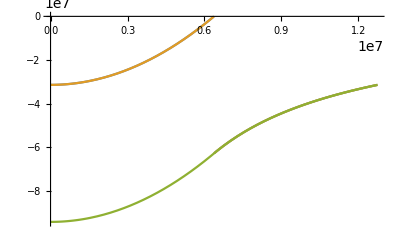

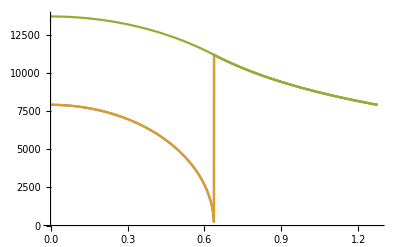

```mathematica
(*Plot[{Veff[#,0.001943801652892562,1,220 10^3]&[r],Veff[#,0.2352,1,20 10^3]&[r],Veff[#,0,1,20 10^3]&[r]},{r,0,2 "rE"/.EarthRepl},PlotRange->All]*)
Plot[{Veff[#,ϕmax[220 10^3],1,220 10^3]&[r],Veff[#,ϕmax[20 10^3],1,20 10^3]&[r],Veff[#,0,1,20 10^3]&[r]},{r,0,2 "rE"/.EarthRepl},PlotRange->All]
Plot[{√(-2Veff[#,ϕmax[220 10^3],1,220 10^3])&[r],√(-2Veff[#,ϕmax[20 10^3],1,20 10^3])&[r],√(-2Veff[#,0,1,20 10^3])&[r]},{r,0,2 "rE"/.EarthRepl},PlotRange->All]
(*-2Veff[#,0.01,1,220 10^3]&["rE"/.EarthRepl]
√(-2Veff[#,0.001,1,20 10^3]&["rE"/.EarthRepl])*)
```

```mathematica
ϕmax[20 10^3]//N
Veff[#,ϕE,vmean,qD]&["rE"/.EarthRepl]
```

0.2352

-6.272×10^7+2/3 qD vmean^2 ϕE

```mathematica
Veff[#,ϕmax[220 10^3],220 10^3,1]&["rE"/.EarthRepl]
```

0.

```mathematica
ϕmax[20 10^3]//N
```

0.2352

```mathematica
Manipulate[Plot[Veff[#,ϕE,20 10^3,1]&[r],{r,0,2 "rE"/.EarthRepl},PlotRange->All],{ϕE,0,ϕmax[20 10^3]}]
```

ReplaceAll::reps: {Constants`EarthRepl} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value 2 rE/.Constants`EarthRepl in {r,0,2 rE/.Constants`EarthRepl} is not a machine-sized real number.

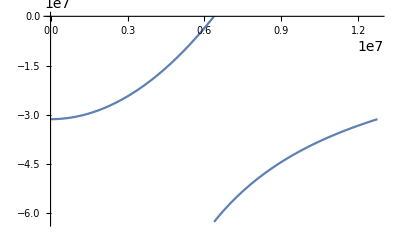

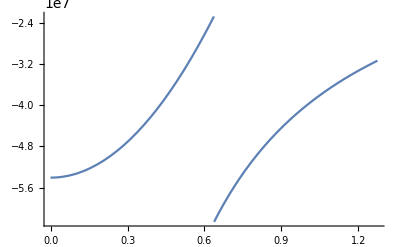

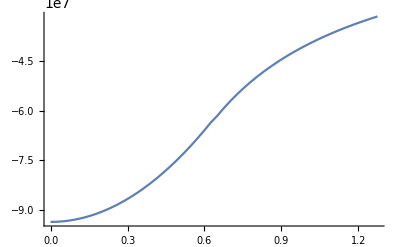

-Graphics-

```mathematica
Do[Print@Plot[{Veff[#,ϕmax[20 10^3],20 10^3,1]&[r],Veff[#,0.15,20 10^3]&[r],Veff[#,0.0015,20 10^3]&[r],Veff[#,0.0015,20 10^3]&[r]}[[i]],{r,0,2 "rE"/.EarthRepl},PlotRange->All],{i,4}]
```

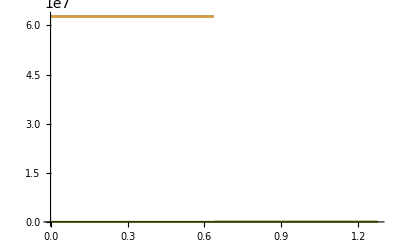

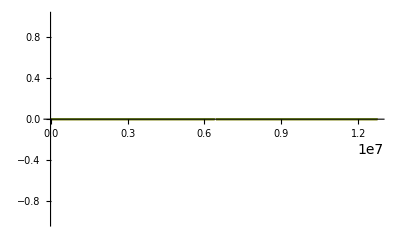

```mathematica
Plot[{Veff[#,ϕmax[220 10^3],220 10^3,1,False]&[r],Veff[#,ϕmax[20 10^3],20 10^3,1,False]&[r],Veff[#,0,20 10^3,1,False]&[r]},{r,0,2 "rE"/.EarthRepl},PlotRange->All]
Plot[{Re@√(-2Veff[#,ϕmax[220 10^3],220 10^3,1,False]&[r]),Re@√(-2Veff[#,ϕmax[20 10^3],20 10^3,1,False]&[r]),Re@√(-2Veff[#,0,20 10^3,1,False]&[r])},{r,0,2 "rE"/.EarthRepl},PlotRange->All]
```

#### EL and Δr total

```mathematica
dc[bE_] := 2 √(("rcore")^2-bE^2)/.Constants`EarthRepl (*path length in the core for given impact parameter*)
dE[bE_] := 2 √(("rE")^2-bE^2)/.Constants`EarthRepl (*path length through the earth*)
dM[bE_]:= If[(("rcore")^2/.Constants`EarthRepl)>bE^2,dE[bE] - dc[bE],Re[dE[bE]]](*path length through the Mantle, iff condition is satisfied does it go through the core*)
```

```mathematica
Clear[GetTotalELFunction]
GetTotalELFunction[ElectronicσDicsts_,NuclearσDicts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts,NuclearσDicts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;

(*Returns: ΔE[bE,vχ]*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
Clear[GeteELFunction]
GeteELFunction[ElectronicσDicsts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
Clear[GetNucELFunction]
GetNucELFunction[NuclearσDicts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[NuclearσDicts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
EK[mχ_,vχ_] :=1/2 mχ vχ^2
ΔrTotbyκsquared[mχ_,vχ_,bE_,ΔEfunc_,y_:10^-2]:=Re[dE[bE] y EK[mχ,vχ]/ΔEfunc[bE,vχ] ]
```

#### Weak Capture Regime Trajectory - Linear

```mathematica
(*Clear[GetWeakCaptureTrajectory]
GetWeakCaptureTrajectory[mχ_,vχE_,bE_,κ_,ELfunc_]:=Module[{RE,lsol,ldom,voft},
(*this version crashes*)
(*use get GetWeakCaptureProbability* with this and GetCaptureRateOldTraj*)
RE = dE[bE];(*path length through the Earth*)
lsol=l/.NDSolve[{D[l[t],{t,2}]==-1/mχ κ^2("JpereV"/.Constants`SIConstRepl)ELfunc[√(bE^2+l[t]^2),l'[t]],l'[0]==vχE,l[0]==-RE/2,WhenEvent[l[t]==RE/2,"StopIntegration"]},l,{t,0,10^4}][[1]];(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=lsol["Domain"][[1]];
(*Print["endpoint vs max"];
Print[lsol[ldom[[2]]]];
Print[RE/2];*)
voft=lsol';
<|"l(t)"->lsol,"v(t)"->voft,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]*)
```

```mathematica
Clear[GetWeakCaptureTrajectoryinv]
GetWeakCaptureTrajectoryinv[mχ_,vχE_,bE_,κ_,ELfunc_]:=Module[{RE,vsol,ldom,voft},
(*use get GetWeakCaptureProbability*fromv with this and GetCaptureRate*)
(*first order solution for trajectory*)
RE = dE[bE];(*path length through the Earth*)
vsol=v/.NDSolve[{D[v[l],l]==-1/(mχ v[l])κ^2("JpereV"/.Constants`SIConstRepl)ELfunc[√(bE^2+l^2),v[l]],v[0]==vχE,WhenEvent[v[l]<="vesc"/.Constants`EarthRepl,"StopIntegration"]},v,{l,-RE/2,RE/2}][[1]];
(*vsol=v/.NDSolve[{D[v[l],l]==-(κ^2("JpereV"/.Constants`SIConstRepl))/mχELfunc[√(bE^2+l^2),v[l]],v[0]==vχE},v,{l,-RE/2,RE/2}][[1]];*)(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=vsol["Domain"][[1]];

(*Print[vsol["Domain"]];*)

<|"v(l)"->vsol,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]
```

```mathematica
Clear[GetWeakCaptureTrajectoryinvFE]
GetWeakCaptureTrajectoryinvFE[mχ_,vχE_,bE_,κ_,ELfunc_,N_:100]:=Module[{RE,h,vofls,vsol,ldom,voft},
(*use get GetWeakCaptureProbability*fromv with this and GetCaptureRate*)
(*Forward Euler solution for trajectory*)

RE = dE[bE];(*path length through the Earth*)
h=RE/N;
vofls=Table[{h s-RE/2,0},{s,N}];
vofls[[1,2]]=vχE;

Do[
(*vofls[[s+1,2]]=vofls[[s,2]]-h(κ^2("JpereV"/.Constants`SIConstRepl))/(mχ vofls[[s,2]])ELfunc[√(bE^2+vofls[[s,1]]^2),vofls[[s,2]]];*)(*I don't think this JpereV should be there.*)
vofls[[s+1,2]]=vofls[[s,2]]-h κ^2/(mχ vofls[[s,2]])ELfunc[√(bE^2+vofls[[s,1]]^2),vofls[[s,2]]];
If[vofls[[s+1,2]]<="vesc"/.Constants`EarthRepl,Break[]];
,{s,N-1}]; (*forward euler for dv/dl=-1/(Subscript[m, χ] v)dE/dl - (ie. from energy conservation / Raleigh-Lagrange Formalism)*)

vsol=Interpolation[vofls]; (*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of length.*)
ldom=vsol["Domain"][[1]];

(*Print[vsol["Domain"]];*)

<|"v(l)"->vsol,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]
```

#### Weak Capture Regime Trajectory - w Potential - Runge Kutta

```mathematica
Clear[GetWeakCaptureTrajectoryinvRK2wPotential]
GetWeakCaptureTrajectoryinvRK2wPotential[mχ_,vχE_,bE_,κ_,ELfunc_,Vofr_:Vgrav,N_:30]:=Module[{rE,Δl,E0,L0,steps,traj,ti,l,r,v,vr,ΔE,L,LogΔL,Lcomped,vsol,ldom,lsol,rdom,voft,rfinal(*,vfinal,vesc*),lMC1,lMC2,lMC},
(*slightly better than FW for conserved quantities, not quite an actual RK2*)
(*
ELfunc - dE/dl
Vofr - (V(r))/mχ
*)

rE="rE"/.Constants`EarthRepl;
Δl=rE/N; (*Δl*)

E0 = mχ/2 vχE^2 +mχ Vofr[rE];
L0 = mχ vχE bE;

traj={<|"l"->0,"r"->rE,"v"->vχE,"vr"->-vχE √(1 - (bE/rE)^2),"ΔE"->0,"V"->mχ Vofr[rE],"L"->L0,"LogΔL"->0(*,"Lcomped"->L0*)|>};
(*initialize list of points along trajectory at Earth's surface
	l - Path length
	r - Distance from Earth's centre
	vχ - aDM speed
	vr - radial aDM speed (initially pointing inward)
	ΔE - Energy lost from dissipation
	L - Angular Momentum
	LogΔL - Log of time dependent part of L 
*)

steps = 0;
Do[
steps++;
ti = traj[[-1]];(*current trajectory point*)

l = ti["l"]+Δl;
(*r = Abs[ti["r"]+Δl ti["vr"]/ti["v"]];*)
r = ti["r"]+Δl ti["vr"]/ti["v"];

If[E0- mχ Vofr[r]-ti["ΔE"]< 0,Break[]]; (*numerical, weaker than the below - will be satisfied when v<0, above will be when v<vesc*)
v = √(2/mχ(E0 - mχ Vofr[r] - ti["ΔE"]) );(*this choice of incrementation, preserves energy but wildly violates L conservation / behaviour*)

ΔE = ti["ΔE"] + Δl κ^2 ELfunc[r,v];

LogΔL = ti["LogΔL"]+ (Δl κ^2 ELfunc[r,v])/(mχ v^2);

L = L0 E^-LogΔL;

vr = ti["vr"] + Δl ((v^2-ti["vr"]^2)/(r v) - (mχ Vofr'[r])/(mχ v)-ti["vr"]/(mχ v^2)κ^2 ELfunc[r,v]);
(*vr = ti["vr"] + Δl ((ti["v"]^2-ti["vr"]^2)/(ti["r"] ti["v"]) - (mχ Vofr'[ti["r"]])/(mχ ti["v"])-ti["vr"]/(mχ ti["v"]^2)κ^2 ELfunc[ti["r"],ti["v"]]);*)
(*vr = ti["vr"] + Δl (L^2/(r^3 mχ^2) - (mχ Vofr'[r])/(mχ v)-ti["vr"]/(mχ v^2)κ^2 ELfunc[r,v]);*)(*assumes ELfunc > 0, so we include - for dissipation*)
(*vr=Sign[ti["vr"]] √(v^2-L^2/(mχ^2 r^2));*)

If[vr/ti["vr"]<0 ,vr=-ti["vr"]];(*vr has changed sign, just take vr to be the same as it was on the previous step with a new sign, avoids the numerical instability from very small r at low impact parameter*)

If[r<0,r = - r;vr=-ti["vr"]]; (*same as above, past near (within Δl of) Earth's centre and is propagating towards surface*)

(*If[vr>10^7,Print["t1 ",(v^2-ti["vr"]^2)/(r v), "\nt2 ",(mχ Vofr'[r])/(mχ v),"\nt3 ",ti["vr"]/(mχ v^2)κ^2 ELfunc[r,v],"\nΔl ",Δl,"\nti[vr]",ti["vr"]]];*)

(*L=mχ r √(v^2-vr^2);(*this choice of incrementation, preserves energy but wildly violates L conservation / behaviour*)*)

(*If[r>rE,Break[]];*)
AppendTo[traj,<|"l"->l,"r"->r,"v"->v,"vr"->vr,"ΔE"->ΔE,"V"->mχ Vofr[r],"L"->L,"LogΔL"->LogΔL(*,"Lcomped"->Lcomped*)|>];

(*Print[mχ/2 v^2+ mχ Vofr[r]];
Print[ mχ Vofr[r]];*)

If[mχ/2 v^2+ mχ Vofr[r]< 0,Break[]];(*particle is captured, ie. bound to the earth, placed after the append statement so that at least one additional point is added. This is needed for the captured condition used further down the pipeline in the case where initial conditions already imply the particle is bound.*)


(* should we remove the append in cases where it's captured right at the surface???? 
no need, all good v_⊥ is irrelevant for capture calculation. *)

If[r>rE,Break[]];
,{s,3N}];(*will break once reaches surface (<~ 2 N) this is just a buffer*)

If[Max[Abs[(("mχ")/2("v")^2+"V"+"ΔE")/E0-1]/.traj]>0.20,Print["Energy conservation has been violated by more than 20% in Forward Euler: ",Max@Abs[(("mχ")/2("v")^2+"V"+"ΔE")/E0-1]/.traj]];

vsol=Quiet@Interpolation[{"l","v"}/.traj]; 
ldom=vsol["Domain"][[1]];

lsol = Quiet@Interpolation[{"l","r"}/.traj];
rdom = lsol["Domain"][[1]];

rfinal = "r"/.traj[[-1]]; (*this is the capture condition - if we stop before we reach the surface, we are captured, otherwise we have left the Earth with E>0 so motion is unbounded. *)

(*values of l where particle crosses mantle-core boundary*)
If[rfinal>"rE"/.Constants`EarthRepl,
(*passes completely through the earth, so approximately symmetric about the l domain. *)
If[Min["r"/.traj]<"rcore"/.Constants`EarthRepl,
(*particle passes through the core*)
lMC1 = l/.Quiet@FindRoot[lsol[l]-"rcore"/.Constants`EarthRepl,{l,rdom[[2]]/4,rdom[[1]],rdom[[2]]/2}];
lMC2 = l/.Quiet@FindRoot[lsol[l]-"rcore"/.Constants`EarthRepl,{l,(3rdom[[2]])/4,rdom[[2]]/2,rdom[[2]]}];
lMC={lMC1,lMC2};,
(*doesn't pass through the core (No Core)*)
lMC={"NC"}
],
(*It's captured somewhere, so we won't need to distinguish between crust and core for since we won't compute hard capture.*)
lMC = {"Cap"}
];

<|"v(l)"->vsol,"domain"->ldom,"r(l)"->lsol,"rdom"->rdom,"traj"->traj,"κ"->κ,"bE"->bE,"mχ"->mχ,"vχE"->vχE,"E0"->E0,"L0"->L0,"steps"->steps,"rfinal"->rfinal,"lMCs"->lMC,"V(r)"->Function[{r},mχ Vofr[r]],"N"->N|>
]
```

### Weak Capture Probabilities

#### Weak Capture Regime Capture Interaction Length - e (not used in pipeline)

```mathematica
Clear[GetWeakCaptureInteractionLength]
GetWeakCaptureInteractionLength[σDict_]:= Module[{vχmin,mχ,ωmin,params,regionindex,σdom,ωcapture,δξ,ξofωandvχt,ωmaxofvχt,dσdERoftandω,σofvχandωmin,λinvofχ},
ωmin="ωmin"/.σDict;
params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
regionindex = "regionindex"/.σDict;
σdom=("σofξf"/.σDict)["Domain"];

vχmin=Max[3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params,"vesc"/.Constants`EarthRepl]; (*restrict minimum velocity according to minimum velocity of interpolation (see energy loss package), and the escape velocity*)

ξofωandvχt=EnergyLoss`ξofωandvχ[#1,ωmin,#2,mχ,params]&;
ωmaxofvχt=EnergyLoss`ωmaxofvχ[#,mχ,params]&;

σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@(ξofωandvχt[#2,#1])]])&;

ωcapture = 1/(2 ("ℏ"/.params))mχ (#^2 - ("vesc"/.Constants`EarthRepl)^2)&; (*energy transfer needed to capture the particle*)

λinvofχ=If[#>vχmin && ωmaxofvχt[#]>ωcapture[#]&&(ξofωandvχt[ωcapture[#],#])>10^σdom[[2,1]],("ne"/.params)σofvχandωmin[#,ωcapture[#]],0]&; (*must have v > minimum velocity allowed, must have maximum possible energy transfer greater than energy needed to capture, and must have that energy transfer be in the domain of the interpolation function*)

λinvofχ
]
```

```mathematica
Clear[GetTotaleWeakCaptureInteractionLength]
GetTotaleWeakCaptureInteractionLength[σDicts_]:=Module[{},
Total@Table[GetWeakCaptureInteractionLength[σDicts[[i]]][#],{i,Length[σDicts]}]&
]
```

#### Weak Capture Regime Capture Interaction Length - Nuc (not used in pipeline)

```mathematica
Clear[GetWeakCaptureInteractionLengthNuc]
GetWeakCaptureInteractionLengthNuc[σDict_]:= Module[{vχmin,mχ,mN,ωmin,params,NucleusParams,regionindex,σdom,ωcapture,δξ,ξofωandvχt,ωmaxofvχt,dσdERoftandω,σofvχandωmin,λinvofχ},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
mN = "mN"/.σDict;
regionindex = "regionindex"/.σDict;
σdom=("σofξf"/.σDict)["Domain"];

(*vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; *)
vχmin=Max[3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params,"vesc"/.Constants`EarthRepl];(*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
(*vχ=If[#>vχmin,#,0]&;*)
(*χtraj=("l(t)"/.vDict);*)

(*ξofωandvχt=Abs[EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]-δξ]&;*)
(*ξofωandvχt=Abs[EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]]&;*)
ξofωandvχt=EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]&;
ωmaxofvχt=EnergyLoss`ωmaxNuc[#,mχ,mN,params]&;

(*dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&; (*not currently used*)*)

(*σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@(Min[ξofωandvχt[#2,#1],1-δξ])]])&;*)
σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@(ξofωandvχt[#2,#1])]])&;

(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (#^2 - ("vesc"/.Constants`EarthRepl)^2)&; (*energy transfer needed to capture the particle*)


(*Print[("σofξf"/.σDict)["Domain"]];
Print@Plot[Log10@(ξofωandvχt[ωcapture[#],#])&[vχ],{vχ,"vesc"/.EarthRepl,5+"vesc"/.EarthRepl}];
Print[Plot[Log10@(ξofωandvχt[ωcapture[#],#])-σdom[[2,1]]&[vχ],{vχ,"vesc"/.EarthRepl,5+"vesc"/.EarthRepl}]];

With[{vχ=1.0001 "vesc"/.EarthRepl},
Print["vχmin"];
Print[vχ-vχmin];
Print["ωmaxofvχ-ωcapture"];
Print[ωmaxofvχt[vχ]-ωcapture[vχ]];
Print["λ^-1"];
Print[("nI"/.NucleusParams)σofvχandωmin[vχ,ωcapture[vχ]]];
Print["ξofωandvχs"];
Print[Log10@ξofωandvχt[ωcapture[vχ],vχ]];
Print[Log10@ξofωandvχt[ωmaxofvχt[vχ],vχ]]];*)

λinvofχ=If[#>vχmin && ωmaxofvχt[#]>ωcapture[#]&&(ξofωandvχt[ωcapture[#],#])>10^σdom[[2,1]],("nI"/.NucleusParams)σofvχandωmin[#,ωcapture[#]],0]&;
(*λinvofχ=If[#>vχmin ,("ne"/.params)σofvχandωmin[#,ωcapture[#]],0]&; *)(*if v is greater than the lowest allowable velocity (set by ωmin - the lowest allowable energy transfer), and the maximum possible energy transfer (set by kinetic energy) is greater than energy needed to capture (always true),
get the INVERSE interaction length / cross-section to transfer at least ωcapture to the system and have energy less than the escape velocity*)

λinvofχ
]
```

```mathematica
Clear[GetTotalNucWeakCaptureInteractionLength]
GetTotalNucWeakCaptureInteractionLength[σDicts_]:=Module[{},
Total@Table[GetWeakCaptureInteractionLengthNuc[σDicts[[i]]][#],{i,Length[σDicts]}]&
]
```

#### Weak Capture Regime Capture Probability - w Potential - position dependent v_esc - e

```mathematica
Clear[GetWeakCaptureProbabilitywPot]
GetWeakCaptureProbabilitywPot[vDict_,σDict_,ELTotalinE_:0]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,ldom,ELofl,κ,regionindex,σdom,vesc,ωcapture,δξ,ξofωandl,ωmaxofl,dσdERoftandω,σoftandωmin,rCore,rE,lcore,lcrust,λinvoft,vbound1,vbound2,λintegrand,integralofλinvwrtr},
ωmin="ωmin"/.σDict;
params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.vDict);
(*ldom = "domain"/.vDict;*)
κ=("κ"/.vDict);
regionindex = "regionindex"/.σDict; (*1 in crust, 2 in core*)
σdom=("σofξf"/.σDict)["Domain"];

bE=("bE"/.vDict);(*impact parameter*)
rCore="rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;
vχraw=("v(l)"/.vDict);

vχmin=Max[3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params,vesc[#]]&;
vχ=If[vχraw[#]>vχmin[#],("v(l)"/.vDict)[#],0]&;
(*bE=("bE"/.vDict);(*impact parameter*)*)

ldom = If[#[[2]]>=(2 √(rE^2-bE^2)),{#[[1]],(*0.96*) 2 √(rE^2-bE^2)},#]&["domain"/.vDict];
(*vesc=Function[{l},√(-(2("V(r)"/.vDict)[("r(l)"/.vDict)[l]])/mχ)];*)
(*vesc=Function[{l}, If[#!=0,#,("vesc")/10^4/.Constants`EarthRepl]&@(Re@√(-(2("V(r)"/.vDict)[("r(l)"/.vDict)[l]])/mχ))];(*if vesc^2 < 0, then set it to a small positive value (we assume flat potential in the Earth)*)*)

(*vesc=Function[{l}, If[#!=0,#,0]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];(*if vesc^2 < 0, then take vesc -> 0.*)*)

(*vesc=Function[{l}, If[#!=0,#,√(2/mχ ELTotalinE(1-l/(2 √(rE^2-bE^2))))]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)
(*vesc=Function[{l}, If[#!=0,#,√(2/mχ ELTotalinE[bE,vχraw[l]](1-l/(2 √(rE^2-bE^2))))]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)(*if vesc^2 < 0, then take vesc -> √(2/mχ Subscript[ΔE, c]). Where Subscript[ΔE, c] is a characteristic value for the EL expected in the remainder of the trajectory through the Earth. Since we assume that the potential is flat for negative vesc^2, we can just get an estimate based on the radius in the Earth, the impact parameter, and the total energy we expect to lose in the Earth. 

It is critical to include this since for nuclear, if vesc^2<0 aDM cannot come to rest through a single hard nuclear scatter.*)

ELofl=Function[{l},Re@√2/mχ ELTotalinE[bE,vχraw[l]]If[#>0,#,0]&@(1-l/(2 √(rE^2-bE^2)))(*0*)];
(*vesc=Function[{l}, If[#!=0,#,If[ELofl[l]!=0,ELofl[l],ELofl[0.99 2 √(rE^2-bE^2)]]]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)

vesc=Function[{l}, If[#!=0,#,ELofl[l]]&@(Re@√(-1/mχ 2("V(r)"/.vDict)[If[("r(l)"/.vDict)[l]<=rE,("r(l)"/.vDict)[l],rE]]))]; (*if vesc^2 < 0, then take vesc -> √(2/mχ Subscript[ΔE, c]). Where Subscript[ΔE, c] is a characteristic value for the EL expected in the remainder of the trajectory through the Earth. Since we assume that the potential is flat for negative vesc^2, we can just get an estimate based on the radius in the Earth, the impact parameter, and the total energy we expect to lose in the Earth. 

It is critical to include this since for nuclear, if vesc^2<0 aDM cannot come to rest through a single hard nuclear scatter.*)(* *** DIFF *)



ξofωandl=EnergyLoss`ξofωandvχ[#1,ωmin,("v(l)"/.vDict)[#2],mχ,params]&;
ωmaxofl=EnergyLoss`ωmaxofvχ[("v(l)"/.vDict)[#1],mχ,params]&;

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandl[#2,#1]]])&;

ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - vesc[#]^2)&;

λinvoft=If[vχraw[#]>vχmin[#] && ωmaxofl[#]>ωcapture[#]&&(ξofωandl[ωcapture[#],#])>10^σdom[[2,1]],κ^2("ne"/.params)σoftandωmin[#,ωcapture[#]],0]&;

(*find the points where capture goes to 0 due to large velocity (a result of acceleration), if the region is too close to the boundary, we need to integrate over them more carefully since mathematica can miss it. *)
vbound1 =Quiet@Check[ l/.FindRoot[ωmaxofl[#]-ωcapture[#]&[l],{l,ldom[[2]]/4,ldom[[1]],ldom[[2]]/2}],ldom[[2]]/2];
vbound2= Quiet@Check[l/.FindRoot[ωmaxofl[#]-ωcapture[#]&[l],{l,(3ldom[[2]])/4,ldom[[2]]/2,ldom[[2]]}],ldom[[2]]/2];

rCore="rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

λintegrand[l_?NumericQ]:=λinvoft[l];

(*Print[ωmin];
Print[vesc[(ldom[[1]]+ldom[[2]])/2]];
Print@Plot[vesc[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"vesc"];
Print@Plot[vχraw[l],{l,ldom[[1]],ldom[[2]]}];
Print@Plot[vχmin[l],{l,ldom[[1]],ldom[[2]]}];
Print@Plot[λintegrand[l],{l,ldom[[1]],ldom[[2]]}];*)

If[vDict["lMCs"]=={ "NC"},
(*Doesn't pass through the core, just integrate*)
If[regionindex==2,
(*material is in the core, return 0*)
Return[0,Module],
(*material is in the mantle, just integrate*)
integralofλinvwrtr=Quiet@Check[#[12],Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];#[15]]&[Function[{MR},If[vbound1/(ldom[[2]]-ldom[[1]])<10^-2||1-vbound2/(ldom[[2]]-ldom[[1]])<10^-2,NIntegrate[λintegrand[l],{l,ldom[[1]],vbound1},PrecisionGoal->3,MaxRecursion->MR,AccuracyGoal->3]+NIntegrate[λintegrand[l],{l,vbound2,ldom[[2]]},PrecisionGoal->3,MaxRecursion->MR,AccuracyGoal->3],NIntegrate[λintegrand[l],{l,ldom[[1]],ldom[[2]]},PrecisionGoal->3,MaxRecursion->MR,AccuracyGoal->3]]]];
],
(*Passes through the core*)
If[regionindex==2,
(*material is in the core, integrate between the two Mantle-Core boundary points*)
integralofλinvwrtr=Quiet@Check[#,Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];#]&[NIntegrate[λintegrand[l],{l,vDict["lMCs"][[1]],vDict["lMCs"][[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]];,
(*material is in the mantle, integrate over the regions before and after the core, then add*)
integralofλinvwrtr=Quiet@Check[#,Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];#]&[NIntegrate[λintegrand[l],{l,ldom[[1]],vDict["lMCs"][[1]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]+NIntegrate[λintegrand[l],{l,vDict["lMCs"][[2]],ldom[[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]];
]
];

integralofλinvwrtr
]
```

#### Weak Capture Regime Capture Probability - w Potential - position dependent v_esc - Nuc

```mathematica
Clear[GetWeakCaptureProbabilityNucwPot]
GetWeakCaptureProbabilityNucwPot[vDict_,σDict_,ELTotalinE_:0]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,NucleusParams,ldom,ELofl,κ,regionindex,σdom,mN,ωcapture,vesc,δξ,ξofωandl,ωmaxofl,dσdERoftandω,σoftandωmin,λinvoft,λintegrand,vbound1,vbound2,rCore,rE,lcore,lcrust,integralofλinvwrtr},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.vDict);
κ=("κ"/.vDict);
mN = "mN"/.σDict;
regionindex = "regionindex"/.σDict;
σdom=("σofξf"/.σDict)["Domain"];

bE=("bE"/.vDict);(*impact parameter*)
rCore="rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;
(*vesc=Function[{l},√(-(2("V(r)"/.vDict)[("r(l)"/.vDict)[l]])/mχ)]; *)
vχraw=("v(l)"/.vDict);

ldom = If[#[[2]]>=(2 √(rE^2-bE^2)),{#[[1]],(*0.96*) 2 √(rE^2-bE^2)},#]&["domain"/.vDict];
(*ldom="domain"/.vDict;*)

(*ldom={("domain"/.vDict)[[1]],(l/.FindRoot[("r(l)"/.vDict)[l]-rE,{l,(3("domain"/.vDict)[[2]])/4,(("domain"/.vDict)[[2]])/2,("domain"/.vDict)[[2]]}])};*)

(*vesc=Function[{l}, If[#!=0,#,("vesc")/10^4/.Constants`EarthRepl]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)(*if vesc^2 < 0, then set it to a small positive value (we assume flat potential in the Earth)*)

(*vesc=Function[{l}, If[#!=0,#,0]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];(*if vesc^2 < 0, then take vesc -> 0. This shuts off capture for Nuclear, and will be accurate assuming there are no potential barriers between the point in the Earth and the surface - ie. for a flat potential which is what we assume.*)*)

ELofl=Function[{l},Re@√2/mχ ELTotalinE[bE,vχraw[l]]If[#>0,#,0]&@(1-l/(2 √(rE^2-bE^2)))(*0*)];
(*vesc=Function[{l}, If[#!=0,#,If[ELofl[l]!=0,ELofl[l],ELofl[0.99 2 √(rE^2-bE^2)]]]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)

vesc=Function[{l}, If[#!=0,#,ELofl[l]]&@(Re@√(-1/mχ 2("V(r)"/.vDict)[If[("r(l)"/.vDict)[l]<=rE,("r(l)"/.vDict)[l],rE]]))]; (*if vesc^2 < 0, then take vesc -> √(2/mχ Subscript[ΔE, c]). Where Subscript[ΔE, c] is a characteristic value for the EL expected in the remainder of the trajectory through the Earth. Since we assume that the potential is flat for negative vesc^2, we can just get an estimate based on the radius in the Earth, the impact parameter, and the total energy we expect to lose in the Earth. 

It is critical to include this since for nuclear, if vesc^2<0 aDM cannot come to rest through a single hard nuclear scatter.*)(* *** DIFF *)

(*vesc=Function[{l}, If[#!=0,#,0]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)

vχmin=Max[Sqrt[("ℏ" ωmin)/(2 mχ)]/.params,vesc[#]]&;(*minimum allowable velocity given the lower bound on energy transfer *)
(*vχmin=Max[3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params,vesc[#]]&;(*minimum allowable velocity given the lower bound on energy transfer times an order one fudge factor (3)*)*)

vχ=If[vχraw[#]>vχmin[#],("v(l)"/.vDict)[#],0]&;

ξofωandl=EnergyLoss`ξofωNuc[#1,ωmin,("v(l)"/.vDict)[#2],mχ,mN,params]&;(*[ω,l]*)
ωmaxofl=EnergyLoss`ωmaxNuc[("v(l)"/.vDict)[#1],mχ,mN,params]&;

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandl[#2,#1]]])&;(*[l,ω]*)

ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - vesc[#]^2)&; 

(*find a way to estimate the amount of energy we expect to lose through the rest of it's trajectory. Well we computed this. It should be in the module for defining the capture probability distribution.*)

λinvoft=If[vχraw[#]>vχmin[#] && ωmaxofl[#]>ωcapture[#]&&(ξofωandl[ωcapture[#],#])>10^σdom[[2,1]],κ^2("nI"/.NucleusParams)σoftandωmin[#,ωcapture[#]],0]&;

vbound1 =Quiet@Check[ l/.FindRoot[ωmaxofl[#]-ωcapture[#]&[l],{l,ldom[[2]]/4,ldom[[1]],ldom[[2]]/2}],ldom[[2]]/2];
vbound2= Quiet@Check[l/.FindRoot[ωmaxofl[#]-ωcapture[#]&[l],{l,(3ldom[[2]])/4,ldom[[2]]/2,ldom[[2]]}],ldom[[2]]/2];(*find the endpoints along the trajectory such that the aDM is moving slow enough that it could potentially be captured by a hard scatter. *)


λintegrand[l_?NumericQ]:=λinvoft[l];

If[(*{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}==(*{1.7799999999999998*^-26,760.9393510361165,1.274250968*^6,1/1000000000000,"Si Nuc"}*){1.7799999999999998*^-26,760.9393510361165,1.9113445970000003*^6,1/1000000000000,"Si Nuc"},*)
(*internalplot&& 300>("vχE"/.vDict)>100&&("materialname"/.σDict)=="Si Nuc"&&bE>10^5,*)
internalplot&& 30>("vχE"/.vDict)>1&&("materialname"/.σDict)=="Si Nuc"&&bE>10^5,
internalplot=False;
(*Print@FindRoot[("r(l)"/.vDict)[l]-rE,{l,(3ldom[[2]])/4,ldom[[2]]/2,ldom[[2]]}];*)
Print["r(l_max)-rE ",("r(l)"/.vDict)[ldom[[2]]]-rE];
Print[Plot[(("r(l)"/.vDict)[l])/rE,{l,ldom[[1]],ldom[[2]]}]];
Print["vbounds ",{vbound1,vbound2}];
Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];
Print["2√(rE^2)",2 √(rE^2-bE^2)];Print["ldom",ldom];
Print[Plot[Log10@λintegrand[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"λ integrand",PlotRange->All,Mesh->All]];Print@Plot[Log10@ωcapture[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"ωcapture"];Print@Plot[Log10@(vesc[l]^2),{l,ldom[[1]],ldom[[2]]},PlotLabel->"vesc^2",PlotRange->All];
Print@Plot[Log10@ELofl[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"Elofl",PlotRange->All];Print@Plot[Log10@ωmaxofl[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"ωmax",PlotRange->{0,15}];
Print@Plot[Log10@σoftandωmin[l,ωcapture[l]],{l,ldom[[1]],ldom[[2]]},PlotLabel->"σ",PlotRange->All];
Print@Plot[Log10@vχ[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"v"];
Print["v(10^7)",vχ[10^7]];
Print["σdom is ",σdom];
Print["ωmin is ",N[ωmin,10]];
Print[Plot[Log10@ξofωandl[ωcapture[l],l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"ξ(ωcap)"]];
Print[Plot[Boole[σdom[[2,1]]<Log10@ξofωandl[ωcapture[l],l]<σdom[[2,2]]],{l,ldom[[1]],ldom[[2]]},PlotLabel->"ξ(ωcap) domain violated?"]];
Print[Boole[σdom[[2,1]]<Log10@ξofωandl[ωcapture[l],l]<σdom[[2,2]]/.l->10^7]];
Print@Plot[Boole[σdom[[2,1]]<Log10@ξofωandl[ωcapture[l],l]<σdom[[2,2]]]Log10@σoftandωmin[l,ωcapture[l]],{l,ldom[[1]],ldom[[2]]},PlotLabel->"σ w cut",PlotRange->All];
Print[Plot[Boole[σdom[[2,1]]<Log10@ξofωandl[ωcapture[l],l]<σdom[[2,2]]]Log10@λintegrand[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"λ integrand w cut",PlotRange->All]];
Print@Plot[ωmaxofl[l]-ωcapture[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"ωmax-ωcapture"];];



If[vDict["lMCs"]=={ "NC"},(*could use -1 and -2 for No core and Captured*)
(*Doesn't pass through the core, just integrate*)
If[regionindex==2,
(*material is in the core, return 0*)
Return[0,Module],
(*material is in the mantle, just integrate*)
integralofλinvwrtr=Quiet@If[vbound1/(ldom[[2]]-ldom[[1]])<10^-2||1-vbound2/(ldom[[2]]-ldom[[1]])<10^-2,NIntegrate[λintegrand[l],{l,ldom[[1]],vbound1},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]+NIntegrate[λintegrand[l],{l,vbound2,ldom[[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3],NIntegrate[λintegrand[l],{l,ldom[[1]],ldom[[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]];
],
(*Passes through the core*)
If[regionindex==2,
(*material is in the core, integrate between the two Mantle-Core boundary points*)
integralofλinvwrtr=Quiet@Check[#,Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];#]&[NIntegrate[λintegrand[l],{l,vDict["lMCs"][[1]],vDict["lMCs"][[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]];,
(*material is in the mantle, integrate over the regions before and after the core, then add*)
integralofλinvwrtr=Quiet@Check[#,Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];#]&[NIntegrate[λintegrand[l],{l,ldom[[1]],vDict["lMCs"][[1]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]+NIntegrate[λintegrand[l],{l,vDict["lMCs"][[2]],ldom[[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]];
]
];

integralofλinvwrtr
]
```

### Initial Conditions

#### vmax

```mathematica
(*Clear[GetvχMax]
GetvχMax[Pcut_,βD_,mχ_]:=Module[{oneminusCDFvmax,vesc,vmaxsol,vmaxbound=0.2 "c"/.SIConstRepl},
vesc=("vesc"/.Constants`EarthRepl);
oneminusCDFvmax = ⅇ^(1/2 mχ vesc^2 βD) (1+2 ⅇ^(-1/2 mχ vmax^2 βD) √((mχ βD)/(2 π))vmax- Erf[√((mχ βD)/(2 π))vmax] );

(*Integral of MB dist, from Subscript[v, max] to ∞ - so probability of v >= Subscript[v, max]*)
vmaxsol=NSolve[{Pcut==oneminusCDFvmax&&0<vmax<vmaxbound},vmax];

If[(vmaxsol)!={},vmax/.vmaxsol[[1]],vmaxbound](*make sure it's non-relativistic and solve for velocity corresponding to the Pcut*)
]*)
```

```mathematica
Clear[GetvχMax]
GetvχMax[Pcut_,βD_,mχ_,vesc_:("vesc"/.Constants`EarthRepl)]:=Module[{oneminusCDFvmax,vmaxsol,vmaxbound=0.2 "c"/.SIConstRepl},
(*vesc=("vesc"/.Constants`EarthRepl);*)
oneminusCDFvmax = (1+2 ⅇ^(-1/2 mχ vmax^2 βD) √((mχ βD)/(2 π))vmax- Erf[√((mχ βD)/2)vmax] );

(*Integral of MB dist, from Subscript[v, max] to ∞ - so probability of v >= Subscript[v, max]*)
vmaxsol=NSolve[{Pcut==oneminusCDFvmax&&0<vmax<vmaxbound},vmax];

If[(vmaxsol)!={},vmax/.vmaxsol[[1]],vmaxbound](*make sure it's non-relativistic and solve for velocity corresponding to the Pcut*)
]
```

```mathematica
Integrate[ ⅇ^(-1/2 m (v^2) β) √(2/π) v^2 (m β)^(3/2) ,{v,vmax,∞}]
%//Normal//PowerExpand//Simplify
```

ConditionalExpression[((m β)^(3/2) (2 ⅇ^(-1/2 m vmax^2 β) m vmax β+√(2 π) √(m β)-√m √(2 π) √β Erf[(√m vmax √β)/(√2)]))/(m^2 √(2 π) β^2), Re[m β]>0]

1+ⅇ^(-1/2 m vmax^2 β) √m √(2/π) vmax √β-Erf[(√m vmax √β)/(√2)]

```mathematica
Integrate[ ⅇ^(-1/2 m (v^2) β) √(2/π) v^2 (m β)^(3/2) ,{v,0,∞}]
%//Normal//PowerExpand//Simplify
```

ConditionalExpression[1, Re[m β]>0]

1

#### Get vχ grid at earth

```mathematica
(*Clear[GetvχatEarth]
GetvχatEarth[vχMax_,nbs_:10,nvχs_:40,lowerbrat_:(*10^-6*)10^-5,lowervrat_:10^-8]:=Module[{rE,vmin,vχs,bs,bEarth,vrEarth,vχ,χspeedEarth},

    rE = "rE"/.Constants`EarthRepl;
    vmin = "vesc"/.Constants`EarthRepl;
   
vχs = vmin+ 10^Subdivide[ Log10[lowervrat(vχMax-vmin)],Log10@(vχMax-vmin),nvχs];

bs = Subdivide[lowerbrat rE,rE,nbs];

Table[<|"χspeedEarth"->vχs[[i]],"bEarth"->bs[[j]]|>,{i,nvχs},{j,nbs}]
]*)
```

```mathematica
Clear[GetvχatEarth]
GetvχatEarth[vχMax_, vmin_: "vesc"/.Constants`EarthRepl,nbs_:10,nvχs_:40,lowerbrat_:(*10^-6*)10^-5(*10^-4.5*),lowervrat_:10^-10(*10^-8*)]:=Module[{rE,vχs,bs,bEarth,vrEarth,vχ,χspeedEarth},

    rE = "rE"/.Constants`EarthRepl;
   
vχs = vmin+ 10^Subdivide[ Log10[lowervrat(vχMax-vmin)],Log10@(vχMax-vmin),nvχs];

bs = Subdivide[lowerbrat rE,rE,nbs];

Table[<|"χspeedEarth"->vχs[[i]],"bEarth"->bs[[j]]|>,{i,nvχs},{j,nbs}]
]
```

```mathematica
"- can take the real part of vesc (so vmin is 0 when imaginary)?"
"No Need to think more carefully about which velocities to include. For positive vesc, we only include velocities above vesc because that is the minimum velocity of incoming aDM. 

But when vesc goes negative, there is also a lower bound on the incoming aDM because only aDM with a high enough velocity can penetrate the potential barrier. This needs to be taken into account. So it may be the absolute value of vesc that has to be considered. 

well actually no, after passing over the barrier the speed will be reduced, so it can still be 0 after passing over the barrier. The velocity here is the velocity once it reaches the surface, not the original velocity at infinity. The change to the distribution is taken into account when integrating over the flux. 

So upshot I think it is the real part that we want. "
```

```mathematica
N[(("vesc")/10^4/.Constants`EarthRepl)+ 10^Subdivide[ Log10[lowervrat("vesc"-("vesc")/10^4/.Constants`EarthRepl)],Log10@("vesc"-("vesc")/10^4/.Constants`EarthRepl),nvχs]/.lowervrat->10^-8/.nvχs->40,10]
```

{1.120111989,1.12017749,1.120281303,1.120445835,1.120706602,1.121119888,1.121774903,1.122813031,1.124458354,1.127066016,1.13119888,1.137749029,1.148130315,1.164583544,1.190660156,1.2319888,1.297490287,1.401303147,1.565835443,1.826601559,2.239888,2.894902868,3.933031472,5.57835443,8.186015586,12.31888,18.86902868,29.25031472,45.7035443,71.78015586,113.1088,178.6102868,282.4231472,446.955443,707.7215586,1121.008,1776.022868,2814.151472,4459.47443,7067.135586,11200.}

### Get Capture Probability

#### Get Probability

```mathematica
Clear[GetCaptureProbability]
GetCaptureProbability[meDovermpD_,κ_,v0_,σDictsElectronic_,σDictsNuclear_,mpDcap_:True,ϕE_:0]:= Module[{mχ,mpD,meD,qD,βD,Veffofr,rE,vesceff,v0pD,vχMax,ICdict,ELfuncTotalbyκsquared,ELthroughEarthbyκsquared,Δrbyκsquared,RE,TrajDict,vfinal,captured,integralofλinvwrtrE ,integralofλinvwrtrNuc,SurvivalProb,CaptureProb,PDictList={},TrajDictinv,MaxBoltzSuppress=10^-20},

(*Get the capture probability for given microphysics parameters

	mpDcap - [boole] True=> compute capture of dark protons, False => compute capture of dark electrons*)

mχ=Join["mχ"/.σDictsElectronic,"mχ"/.σDictsNuclear];
mχ=If[Length@Union[mχ]==1,mχ[[1]],Print["mχ must be the same in all processes:",mχ];Return[<||>,Module]];

If[mpDcap,
(*True => computing capture rate for dark protons
False => computing capture rate for dark electrons*)
(*mpD = mχ;meD = meDovermpD mχ;,
meD = mχ;mpD =  mχ/meDovermpD;*)
{mpD,meD ,qD} = {mχ, meDovermpD mχ,1};
,
{meD ,mpD,qD}={ mχ, mχ/meDovermpD,-1};
];

(*what we can do to change from p->e is introduce a flag for mpD or meD. Then here we use the σDict for e capture. Then all we need to do is relabel the variables so mpD -> meD, (ie. meD = mχ, mpD = mχ/meDovermpD, with mχ the mass used in the σDicts). We also need to pass this to vχ at Earth and vχMax (can just pass meD instead of mpD). This will also be passed to Get weak capture trajectory*)

βD ="βD"/.v0toβD[ v0,meD,mpD];(*for fixed mχ, this is the only thing that will change for different values of the mpDcap flag*)

(*Veffofr = Veff[#,ϕE,√(3/(βD mχ)),qD]&;*) (*the effective vesc at the surface given both gravitational and dark electrostatic contributions (times 1/m)*)
Veffofr = If[ϕmax[√(3/(βD mχ)),qD]<ϕE,Veff[#,ϕE,√(3/(βD mχ)),qD,False],Veff[#,ϕE,√(3/(βD mχ)),qD,True]]&;(*if vesc^2 < 0, then take potential in the earth to be flat, if not use full gravitational potential.*)

(*Print@Plot[Veffofr[r],{r,0,"rE"/.Constants`EarthRepl}];*)

rE= "rE"/.Constants`EarthRepl;
(*vesceff = Re@vescofr[rE,ϕE,qD,√(3/(βD mχ))];*)
(*vesceff = Re@vescofr[rE,ϕE,√(3/(βD mχ)),qD,False];*)
vesceff = If[#!=0,#,("vesc")/10^4/.Constants`EarthRepl]&@(Re@√(-2 Veffofr[rE]));
(*vesceff = If[#!=0,#,0]&@(Re@√(-2 Veffofr[rE]));*)(*if the real part of vesc ==0 then set it to ~1 ms^-1 for numerical stability*)

(*Print[vesceff];*)
(*Print[ √(-2 Veff[rE,ϕE,√(3/(βD mχ)),qD,False])];
Print[ Re@√(-2 Veff[rE,ϕE,√(3/(βD mχ)),qD,False])];*)

(*vescofr[r_,ϕE_:0,vmean_:2 10^4,qD_:1,wgrav:True]:= √(-2 Veff[r,ϕE,vmean,qD,wgrav])*)

(*Print@ vescofr[rE,ϕE,√(3/(βD mχ)),qD,True];
Print@ Re@vescofr[rE,ϕE,√(3/(βD mχ)),qD,True];
Print@ vescofr[rE,ϕE,√(3/(βD mχ)),qD,False];
Print@vesceff;*)(*escape velocity at earth's surface including electrostatic effects - We take the real part so that vesceff -> 0 when vesc^2<0 (change to distribution is handled in the integration over the flux later on)*)

(*depends on vesc*)
vχMax=GetvχMax[MaxBoltzSuppress,βD,mχ,vesceff]; (*from the above comment, the only difference between pD and eD capture will be velocity range we look at*)

(*depends on vesc*)
 ICdict=Flatten@GetvχatEarth[vχMax,vesceff];(*dictionary of initial conditions at earth*) 

{ELfuncTotalbyκsquared,ELthroughEarthbyκsquared} = {"dEdlofr","ΔEthroughEarth"}/.GetTotalELFunction[σDictsElectronic,σDictsNuclear];

(*Print@ELthroughEarthbyκsquared;*)

(*Monitor[*)

Do[
(*Print@Plot[ELthroughEarthbyκsquared[r,10^5],{r,0,10^7}];*)
Δrbyκsquared=ΔrTotbyκsquared[mχ,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],ELthroughEarthbyκsquared]; 


RE=dE["bEarth"/.ICdict[[n]]];

If[Δrbyκsquared/κ^2>RE/100,
(*on average will loose 100% of kinetic energy as it travels through the earth, if speed is fixed*)

(*depends on vesc*)
TrajDict=GetWeakCaptureTrajectoryinvRK2wPotential[mχ,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ,Veffofr]; 
(*TrajDict=GetWeakCaptureTrajectoryinvFE[mχ,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ];*) 
(*TrajDict=GetWeakCaptureTrajectoryinv[mχ,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ]; *)

(*vfinal= ("v(l)"/.TrajDict)[TrajDict["domain"][[2]]];*)
(*captured=vfinal<"vesc"/.Constants`EarthRepl;*)
(*captured=vfinal<"vesc"/.TrajDict;*)
vfinal= "vfinal"/.TrajDict;
captured = ("rfinal"/.TrajDict)<("rE"/.Constants`EarthRepl);(*stop condition is bounded motion (E<0) so if we exit the Earth the motion is unbounded, otherwise its bounded.*)

If[!captured,
(*allow continuous slowing down, escapes with v>vesc, check if can be captured through hard scatter*)

(*integralofλinvwrtrE = Total@Table[GetWeakCaptureProbabilityfromv[TrajDict,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}];
integralofλinvwrtrNuc = Total@Table[GetWeakCaptureProbabilityNucfromv[TrajDict,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}];*)
integralofλinvwrtrE = Total@Table[GetWeakCaptureProbabilitywPot[TrajDict,σDictsElectronic[[i]],κ^2 ELthroughEarthbyκsquared[#1,#2]&],{i,Length[σDictsElectronic]}];
integralofλinvwrtrNuc = Total@Table[GetWeakCaptureProbabilityNucwPot[TrajDict,σDictsNuclear[[i]],κ^2 ELthroughEarthbyκsquared[#1,#2]&],{i,Length[σDictsNuclear]}];

SurvivalProb =If[integralofλinvwrtrE + integralofλinvwrtrNuc>250,0,N[E^(-(integralofλinvwrtrE + integralofλinvwrtrNuc)),50]];
(*CaptureProb=If[integralofλinvwrtrE + integralofλinvwrtrNuc>250,1,If[N[integralofλinvwrtrE + integralofλinvwrtrNuc,5]<0.001,N[integralofλinvwrtrE + integralofλinvwrtrNuc,5],N[1-E^(-(integralofλinvwrtrE + integralofλinvwrtrNuc)),5]]];*)
CaptureProb=If[integralofλinvwrtrE + integralofλinvwrtrNuc>250,1,If[N[integralofλinvwrtrE + integralofλinvwrtrNuc,50]<0.001,N[integralofλinvwrtrE + integralofλinvwrtrNuc,50],N[1-E^(-(integralofλinvwrtrE + integralofλinvwrtrNuc)),50]]];

AppendTo[PDictList,<|"Psurv"->N[SurvivalProb,50],"Pcap"->Max[CaptureProb,10^-100],"CSDcap"->Boole@captured,"vχE"->"χspeedEarth"/.ICdict[[n]],"bEarth"->("bEarth"/.ICdict[[n]]),"vfinal"->vfinal,"κ"->κ,"mpD"->mpD,"meD"->meD,"mχ"->mχ,"mpDcap"->mpDcap,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"ϕE"->ϕE,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->Max[N[integralofλinvwrtrE,50],10^-100],"PcapNuc"->Max[N[integralofλinvwrtrNuc,50],10^-100],"intλinvE"->integralofλinvwrtrE,"intλinvNuc"->integralofλinvwrtrNuc|>];,


(*allowed continuous slowing down, v<vesc, it's captured*)
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->Boole@True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->vfinal,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"mχ"->mχ,"mpDcap"->mpDcap,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"ϕE"->ϕE,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->10^-100,"intλinvNuc"->10^-100|>](*captured by CSD so take inverse capture length to Subscript[r, E] so that it's integral over the trajectory is ~1, If we are CSD captured, we want to set the inverse hard capture interaction length to be small so that we can use it to distinguish between hard and soft capture*)
];
,
(*call it captured since on average more than 100 percent of KE is lost as it traverses the earth*)
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->Boole@True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->0,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"mχ"->mχ,"mpDcap"->mpDcap,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"ϕE"->ϕE,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->10^-100,"intλinvNuc"->10^-100|>]
];
,{n,Length[ICdict]}
];
(*,n];*)

PDictList
]
```

```mathematica
Clear[IterateGetCaptureProbability]
IterateGetCaptureProbability[meDovermpD_,κs_,v0_,σDictsElectronic_,σDictsNuclear_,mpDcap_:True,ϕE_:0]:= Module[{PDictList={}},

(*Monitor[*)
Do[(*Print["κ is: ",N@κs[[κ]]];*)
PDictList=Join[PDictList,GetCaptureProbability[meDovermpD,κs[[κ]],v0,σDictsElectronic,σDictsNuclear,mpDcap,ϕE]]; (*flag for p->e*)
,{κ,Length[κs]}];
(*,κ];*)

PDictList
]
```

#### Interpolate Capture Probability distributions

```mathematica
Clear[InterpolatePc]
InterpolatePc[PDictList_]:=Module[{Intertable,Interf,κGatheredDicts,mpD,meD,mpDcap,mχ,vχMax,βD,v0,ϕE},

{mpD,meD,mχ,mpDcap,vχMax,βD,v0,ϕE}=Union[{"mpD","meD","mχ","mpDcap","vχMax","βD","v0","ϕE"}/.PDictList][[1]];
κGatheredDicts=Gather[PDictList,(#1["κ"]==#2["κ"])&];
Interf=Table[<|"Pf"->Interpolation[Log10@{{"vχE","bEarth"},"Pcap"}/.κGatheredDicts[[i]],InterpolationOrder->1],"κ"->(Union["κ"/.κGatheredDicts[[i]]][[1]]),"mpD"->mpD,"meD"->meD,"mχ"->mχ,"mpDcap"->mpDcap,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"ϕE"->ϕE,"PfE"->Interpolation[Log10@{{"vχE","bEarth"},"PcapE"}/.κGatheredDicts[[i]],InterpolationOrder->1],"PfNuc"->Interpolation[Log10@{{"vχE","bEarth"},"PcapNuc"}/.κGatheredDicts[[i]],InterpolationOrder->1],"y"->Interpolation[Log10@{{"vχE","bEarth"},"y"}/.κGatheredDicts[[i]],InterpolationOrder->1],"CSDcap"->Interpolation[{Log10@{"vχE","bEarth"},1-2"CSDcap"}/.κGatheredDicts[[i]],InterpolationOrder->1],"intλinvE"->Interpolation[Log10@{{"vχE","bEarth"},Max["intλinvE",10^-100]}/.κGatheredDicts[[i]],InterpolationOrder->1],"intλinvNuc"->Interpolation[Log10@{{"vχE","bEarth"},Max["intλinvNuc",10^-100]}/.κGatheredDicts[[i]],InterpolationOrder->1]|>,{i,Length[κGatheredDicts]}];
Interf
]
```

### Get Total Capture Rate

#### aDM number density

```mathematica
nD0ΛCDM[fD_,mDMtot_] := Module[{ΛCDMrepl,h,ρcritbaumanncm,ρcritbaumannm, n0,mSMtot,ρDM0},
(*mDMtot - [kg] sum of masses of DM species *)

ΛCDMrepl= {"Ωk" ->0.00,"Ωr"->9.4 10^-5, "Ωm"->0.32,"ΩΛ"->0.68,"Ωb"->0.05,"Ωc"->0.27}; (*[] ΛCDM density parameters*)
h= 0.67; (*baumann 1.2.64*)

ρcritbaumanncm = 1.1 10^-5 h^2; (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  (10^6); (*[protons m^-3] ((10^2 cm)/m)^3*) 

n0 = "Ωb" ρcritbaumannm /.ΛCDMrepl;  (*[m^-3] proton / electron number density today*)
mSMtot= "m" + 2000 "m"/.Constants`SIConstRepl;

ρDM0= "Ωc"/"Ωb" n0 mSMtot/.ΛCDMrepl;
ρDM0/mDMtot fD
]
```

```mathematica
naDM[fD_,mDMtot_] := Module[{ρDM},
(*fD - [ ] ionized mass fraction of local DM density in the galaxy
mDMtot - [kg] sum of masses of DM species *)

ρDM = 0.3 GeV cm^-3/.cm->10^-2/.GeV->10^9("JpereV")/("c")^2/.Constants`SIConstRepl;  (*[kg m^-3] Local DM number density today*)

ρDM/mDMtot fD
]
```

#### Flux and NcMax defn

```mathematica
Clear[GetNcMax]
GetNcMax[InterPDicts_,keys_:{"Pf"},mpDcap_:True,vE_:0]:=Module[{tempInterPDicts,Pfs,vescsq,rE,(*vesc,*)tEarth,AEarth,mχ,βD,Pfdom,anisotropyfactor,fintegrand,intregboundaries,dNcMaxdt},
(*Get maximum possible accumulation over the lifetime of Earth, with κ=1

InterPDicts - Probability Associations (output of IterateGetCaptureRate)
keys - a list of Association Keys for Probability Interpolations (function of vχ and bE). If more than one key is given, they will be summed when computing the capture rate. Default value corresponds to the Total capture probability.*)

tempInterPDicts = InterPDicts;

If[AnyTrue[Table[MemberQ[Flatten@Keys@InterPDicts,keys[[k]]],{k,Length[keys]}],!#&],Print["One of these keys is not a valid association for the interpolation dictionary"];Return[0,Module]];
Pfs=keys/.InterPDicts;

rE="rE"/.Constants`EarthRepl;
vescsq=Union[-2Veff[rE,"ϕE",√(3/("βD" "mχ")),If["mpDcap",1,-1]]/.InterPDicts][[1]];
(*vesc = "vesc"/.Constants`EarthRepl;*)
tEarth = 4.543 10^9 (356  24 3600);(*[s] age of the Earth*)
AEarth = 4 π rE^2; (*[m^2] Surface Area of the Earth*)

Do[
mχ="mχ"/.InterPDicts[[i]]; 
βD="βD"/.InterPDicts[[i]];
Pfdom=Union@Table[Pfs[[i,k]]["Domain"],{k,Length[Pfs[[i]]]}];

If[(Dimensions@Pfdom)[[1]]!=1,Print["The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over."];Return[0,Module]];

anisotropyfactor = If[#!=0,E^(-x/2 vE/(√(#^2-vescsq)))Sinh[x]/x/.x->βD mχ vE √(#^2-vescsq) ,1]& ; (* function of vχ *)

Pfdom = Pfdom[[1]];
fintegrand[bE_?NumericQ,vχ_?NumericQ]:=anisotropyfactor[vχ]bE ⅇ^(-1/2 mχ (vχ^2-vescsq) βD)  vχ^3 Sum[10^(Pfs[[i,k]][Log10@vχ,Log10@bE]),{k,Length[Pfs[[i]]]}];(*[s^-1] goes as <Subscript[v, χ]> Subscript[n, aDM] Subscript[A, Earth] so this rate over Subscript[V, Earth] is <Subscript[v, χ]> Subscript[n, aDM] Subscript[R, Earth]^-1 which is what was used in the appendix*)

(*Print[fintegrand[(10^Pfdom[[1,1]]+10^Pfdom[[1,1]])/2,(10^Pfdom[[2,1]]+10^Pfdom[[2,1]])/2]];*)

intregboundaries=If[mpDcap,Table[(10^Pfdom[[1,2]]-10^Pfdom[[1,1]])10^c,{c,-6,-1}],Table[(10^Pfdom[[1,2]]-10^Pfdom[[1,1]])10^c,{c,-8,-1}]]; 
dNcMaxdt=AEarth("nD" √(8 π)  (mχ βD)^(3/2))/rE^2 Quiet@Check[#,Print[{mχ,βD,"κ"/.InterPDicts[[i]]}];#]&[(NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,1]]+intregboundaries[[1]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},PrecisionGoal->3,MaxRecursion->8,AccuracyGoal->3]+Sum[With[{ct=c},NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]]+intregboundaries[[ct-1]],10^Pfdom[[1,1]]+intregboundaries[[ct]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},PrecisionGoal->3,MaxRecursion->8,AccuracyGoal->3]],{c,2,Length[intregboundaries]}]+NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]]+intregboundaries[[-1]],10^Pfdom[[1,2]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},PrecisionGoal->3,MaxRecursion->8,AccuracyGoal->3])];   
(*we break up the integration region because Nuclear capture probability is EXTREMELY sharply peaked near vχ=vesc. Mathematica will ignore this contribution for most of the parameter space if we don't divide up the integration region like this. *)

(* May want to define a function of the integration bounds so this expression isn't so disgusting. *)

If[keys=={"Pf"},
AppendTo[tempInterPDicts[[i]],<|"dNcMaxdt"->dNcMaxdt|>];
AppendTo[tempInterPDicts[[i]],<|"NcMax"->dNcMaxdt tEarth|>];
,
AppendTo[tempInterPDicts[[i]],<|"dNcMaxdt"<>StringJoin[Table["_"<>keys[[k]],{k,Length[keys]}]]->dNcMaxdt|>];
AppendTo[tempInterPDicts[[i]],<|"NcMax"<>StringJoin[Table["_"<>keys[[k]],{k,Length[keys]}]]->dNcMaxdt tEarth|>];
];

,{i,Length[Pfs]}];

tempInterPDicts
]
```

#### Evaporation Rate - w Evap Volume

```mathematica
Clear[GetEvaporationRateVevap]
GetEvaporationRateVevap[σDict_,κ_,vescsq_:("vesc"/.Constants`EarthRepl)^2,mpDcap_:True,Vevapfunc_:"NA"]:= Module[{vχmin,vχmax,vesc,mχ,ωmin,params,regionindex,NucleusParams,mN,nT,βE,ωcapture,δξ,ξmin,ξofωandvχ,ωmaxofvχ,dσdERofvχandω,σofvχandωmin,Ωevapperparticle,Γevappercapturedparticle,vχstωcapisωmax,RegionVolume,ΩevapperparticlewvT,EarthVolume,EvapRescale,fintegrand,intregboundaries,Nvχ=100},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
mN = "mN"/.σDict;
regionindex="regionindex"/.σDict;
βE = {"βcrust","βcore"}[[regionindex]]/.Constants`EarthRepl;(*Earth Temeperature*)
nT = "nI"/.NucleusParams;
EarthVolume =  (4π)/3 ("rE"/.Constants`EarthRepl)^3; 

ξofωandvχ=EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]&;

σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@ξofωandvχ[#2,#1]]])&;

vχmin = 10^(("σofξf"/.σDict)["Domain"][[1,1]]);

vesc = √vescsq//PowerExpand//N;

ξmin = 10^(("σofξf"/.σDict)["Domain"][[2,1]]);

(*Post ωcapture*)
ωmaxofvχ=EnergyLoss`ωmaxNuc[#1,mχ,mN,params]&; (*maximum energy transferable in a collision*)

ωcapture = 1/(2 ("ℏ"/.params))mχ (vesc^2-#^2 )&;(*energy transfered to aDM such that it has v > Subscript[v, esc]*)

vχstωcapisωmax=vχ/.NSolve[ωmaxofvχ[vχ]==ωcapture[vχ],vχ][[2]];(*find the lowest velocity such that aDM can be evaporated through a single scatter*)

EvapRescale=1/(-If[x^2<500,ⅇ^(-1/2 x^2) √(2/π) x,0]+Erf[x/(√2)])/.x->√mχ vesc √βE/.Constants`EarthRepl; (*account for the fact that the MB distribution is truncated, renormalize*)

fintegrand[vT_?NumericQ,vχ_?NumericQ]:=If[StringQ[Vevapfunc],vT^2 E^(-βE 1/2 mN vT^2)((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)vχ^2 E^(-βE 1/2 mχ vχ^2) If[ωmaxofvχ[vχ]>ωcapture[vχ]&&(ξofωandvχ[ωcapture[vχ],vχ])>ξmin,1,0]σofvχandωmin[vχ,ωcapture[vχ]],Vevapfunc[vχ,κ,regionindex]/EarthVolume vT^2 E^(-βE 1/2 mN vT^2)((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)vχ^2 E^(-βE 1/2 mχ vχ^2) If[ωmaxofvχ[vχ]>ωcapture[vχ]&&(ξofωandvχ[ωcapture[vχ],vχ])>ξmin,1,0]σofvχandωmin[vχ,ωcapture[vχ]]];

intregboundaries=If[mpDcap,Table[(vesc-vχstωcapisωmax)10^c,{c,-5,-1}],Table[(vesc-vχstωcapisωmax)10^c,{c,-7,-1}]];(* DIFF !!! *)

ΩevapperparticlewvT=EvapRescale  nT  ((√(mχ mN)βE)/(2 π))^3 4 π 2 π Quiet@(NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax,vχstωcapisωmax + intregboundaries[[1]]},{vT,0,∞},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3]+Sum[NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax+ intregboundaries[[c-1]],vχstωcapisωmax + intregboundaries[[c]]},{vT,0,∞},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3],{c,2,Length[intregboundaries]}]+NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax+ intregboundaries[[-1]],vesc},{vT,0,∞},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3]);

Γevappercapturedparticle=If[StringQ[Vevapfunc],RegionVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,0,"rE"/.Constants`EarthRepl}]; ΩevapperparticlewvT RegionVolume/EarthVolume,ΩevapperparticlewvT];  (*Γκ^2 corresponds to Revp in appendix*)(*Assumes homogeneously distributed aDM in the Earth*)

<|"Γ"->Γevappercapturedparticle,"regionindex"->regionindex|>
]
```

```mathematica
Clear[IterateGetEvaporationRateVevap]
IterateGetEvaporationRateVevap[NuclearσDicts_,κ_,vescsq_:("vesc"/.Constants`EarthRepl)^2,mpDcap_:True,Vevapfunc_:"NA"]:=Module[{Γlist={},ΓTotal},
Monitor[
Do[
AppendTo[Γlist,GetEvaporationRateVevap[NuclearσDicts[[n]],κ,vescsq,mpDcap,Vevapfunc]],
{n,Length[NuclearσDicts]}
];
,n];
ΓTotal=Total[Γlist[[;;,1]]];

<|"ΓTotal"->ΓTotal,"Γs"->Γlist|>
]
```

#### Evaporation Rate Electronic - w Evap Volume

```mathematica
Clear[GetEvaporationRateendVevap]
GetEvaporationRateendVevap[σDict_,κ_,(*Vevapfunc_:"NA",mpDcap_:True*)vescsq_:("vesc"/.Constants`EarthRepl)^2,mpDcap_:True,Vevapfunc_:"NA"]:= Module[{vχmin,vχmax,vesc,mχ,ωmin,params,regionindex,mT,nT,vF,(*vesc,*)vTm,vTp,βE,ωcapture,δξ,ξmin,ξofωandvχt,ωmaxofvχt,dσdERofvχandω,σofvχandωmin,Ωevapperparticle,Γevappercapturedparticle,vχstωcapisωmax,RegionVolume,ΩevapperparticlewvT,EarthVolume,EvapRescale,fintegrand,intregboundaries,PLOT=False},

params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
mT = "m"/.σDict;
regionindex="regionindex"/.σDict;
βE = {"βcrust","βcore"}[[regionindex]]/.Constants`EarthRepl;(*Earth Temeperature*)
nT = "ne"/.params;
vF="vF"/.params;
(*vesc = ("vesc"/.Constants`EarthRepl);*)
EarthVolume =  (4π)/3 ("rE"/.Constants`EarthRepl)^3;

vχmin = Max[10^(("σofξf"/.σDict)["Domain"][[1,1]]),Re[√(vescsq - 8/(mχ βE))]];
vesc = √vescsq//PowerExpand//N;

ξmin = 10^(("σofξf"/.σDict)["Domain"][[2,1]]);


ωmin="ωmin"/.σDict;
ξofωandvχt=EnergyLoss`ξofωandvχnd[#1,ωmin,#2,mχ,params]&;

σofvχandωmin=10^(("σofξf"/.σDict)[Log10@#1,Log10@ξofωandvχt[#2,#1]])&;

ωmaxofvχt=EnergyLoss`ωmaxofvχnd[#1,mχ,params]&; (*maximum energy transferable in a collision*)

ωcapture = 1/(2 ("ℏ"/.params))mχ (vesc^2-#^2 )&;(*energy transfered to aDM such that it has v > Subscript[v, esc]*)

vχstωcapisωmax=vχmin;

EvapRescale=1/(-If[x^2<500,ⅇ^(-1/2 x^2) √(2/π) x,0]+Erf[x/(√2)])/.x->√mχ vesc √βE/.Constants`EarthRepl; (*account for the fact that the aDM MB distribution is truncated, normalize to 1*)


fintegrand[vT_?NumericQ,vχ_?NumericQ]:=If[StringQ[Vevapfunc],vT^2 (fnd[vT/vF]/.params)(((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ))vχ^2 E^(-βE 1/2 mχ vχ^2) If[ωmaxofvχt[vχ]>ωcapture[vχ]&&(ξofωandvχt[ωcapture[vχ],vχ])>ξmin,1,0]σofvχandωmin[vχ,ωcapture[vχ]],Vevapfunc[vχ,κ,regionindex]/EarthVolume vT^2 (fnd[vT/vF]/.params)(((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ))vχ^2 E^(-βE 1/2 mχ vχ^2) If[ωmaxofvχt[vχ]>ωcapture[vχ]&&(ξofωandvχt[ωcapture[vχ],vχ])>ξmin,1,0]σofvχandωmin[vχ,ωcapture[vχ]]]; (* DIFF !!! *)

intregboundaries=If[mpDcap,Table[(vesc-vχstωcapisωmax)10^c,{c,-5,-1}],Table[(vesc-vχstωcapisωmax)10^c,{c,-7,-1}]];

{vTm,vTp}={vF Dielectrics`ζm,vF Dielectrics`ζp}/.params;

ΩevapperparticlewvT=EvapRescale  nT (("D"/.params)/(√(2 π))) ((√(mχ βE))/vF)^3 Quiet@(NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax,vχstωcapisωmax + intregboundaries[[1]]},{vT,vTm,vTp},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3]+Sum[With[{ct=c},NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax+ intregboundaries[[ct-1]],vχstωcapisωmax + intregboundaries[[ct]]},{vT,vTm,vTp},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3]],{c,2,Length[intregboundaries]}]+NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax+ intregboundaries[[-1]],vesc},{vT,vTm,vTp},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3]);

Γevappercapturedparticle=If[StringQ[Vevapfunc],RegionVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,0,"rE"/.Constants`EarthRepl}]; ΩevapperparticlewvT RegionVolume/EarthVolume,ΩevapperparticlewvT]; 

<|"Γ"->Γevappercapturedparticle,"regionindex"->regionindex|>
]
```

```mathematica
Clear[IterateGetEvaporationRateendVevap]
IterateGetEvaporationRateendVevap[ElectronicσDicts_,κ_,vescsq_:("vesc"/.Constants`EarthRepl)^2,mpDcap_:True,Vevapfunc_:"NA"]:=Module[{Γlist={},ΓTotal},
(*Monitor[*)
Do[
If[ElectronicσDicts[[n]]!=<|"NA"->Null|>,
AppendTo[Γlist,GetEvaporationRateendVevap[ElectronicσDicts[[n]],κ,vescsq,mpDcap,Vevapfunc]]],
{n,Length[ElectronicσDicts]}
];
(*,n];*)
ΓTotal=Total[Γlist[[;;,1]]];
<|"ΓTotal"->ΓTotal,"Γs"->Γlist|>
]
```

#### Get Penetration Depth

```mathematica
Clear[GetPenetrationDepthfnofv]
(*the vesc isn't used in the body of the module*)
GetPenetrationDepthfnofv[vχ_,ElectronicσDicts_,NuclearσDicts_]:=Module[{mχ,βC,βM,λinve,λinvNuc,eregiontable,eregiondict,vdom,nT,Nucregiontable,Nucregiondict},

	mχ=Union@Join["mχ"/.ElectronicσDicts,"mχ"/.NuclearσDicts];
	If[Length[mχ]>1,Print["Masses in all σDicts must be equal."];Return[<|"N/A"->Null|>,Module](*,mχ=mχ[[1]]*)];
	
	{βC,βM}={"βcore","βcrust"}/.Constants`EarthRepl;
	
	eregiontable = Gather[ElectronicσDicts,#1["regionindex"]==#2["regionindex"]&];
	eregiondict=Association@Table[Union["regionindex"/.eregiontable[[i]]][[1]]->eregiontable[[i]],{i,Length[eregiontable]}];
	
	λinve =Association@Table[r->Sum[vdom=("σf"/.eregiondict[#2][[o]])["Domain"][[1]];
	nT=("ne"/.eregiondict[#2][[o]]["params"]);If[#1>vdom[[1]]&&#1<vdom[[2]],nT 10^("σf"/.eregiondict[#2][[o]])[#1],0],{o,Length[eregiondict[#2]]}]&[Log10@vχ,r],{r,2}];(*λinve[vχ][r] - r is the regionindex*)
	
	Nucregiontable = Gather[NuclearσDicts,#1["regionindex"]==#2["regionindex"]&];
	Nucregiondict=Association@Table[Union["regionindex"/.Nucregiontable[[i]]][[1]]->Nucregiontable[[i]],{i,Length[eregiontable]}];
	
	λinvNuc=Association@Table[r->Sum[vdom=("σf"/.Nucregiondict[#2][[o]])["Domain"][[1]];
	nT=("nI"/.Nucregiondict[#2][[o]]["NucleusParams"]);If[#1>vdom[[1]]&&#1<vdom[[2]],nT 10^("σf"/.Nucregiondict[#2][[o]])[#1],0],{o,Length[Nucregiondict[#2]]}]&[Log10@vχ,r],{r,2}];(*λinvNuc[vχ][r] - r is the regionindex*)

<|"mχ"->mχ,"λC"->Quiet@Check[(λinve[2]+λinvNuc[2])^-1,10^4"rE"/.EarthRepl],"λM"->Quiet@Check[(λinve[1]+λinvNuc[1])^-1,10^4"rE"/.EarthRepl],"vχ"->vχ,"λinve"->λinve,"λinvNuc"->λinvNuc|>
]
```

```mathematica
(*Clear[GetPenetrationDepth]
(*This is not used in the code*)
GetPenetrationDepth[ElectronicσDicts_,NuclearσDicts_,vesc_:"vesc"/.Constants`EarthRepl]:=Module[{mχ,βC,βM,vbar,λinve,λinvNuc,eregiontable,eregiondict,vdom,nT,Nucregiontable,Nucregiondict},

(* *σDicts should be a single list format (ie. for 1 mass) *)

mχ=Union@Join["mχ"/.ElectronicσDicts,"mχ"/.NuclearσDicts];
If[Length[mχ]>1,Print["Masses in all σDicts must be equal."];Return[<|"N/A"->Null|>,Module](*,mχ=mχ[[1]]*)];

{βC,βM}={"βcore","βcrust"}/.Constants`EarthRepl;

vbar = <|2->Log10@Max[√(2/(mχ βC)),vesc],1->Log10@Max[√(2/(mχ βM)),vesc]|>;

eregiontable = Gather[ElectronicσDicts,#1["regionindex"]==#2["regionindex"]&];
eregiondict=Association@Table[Union["regionindex"/.eregiontable[[i]]][[1]]->eregiontable[[i]],{i,Length[eregiontable]}];

λinve =Association@Table[r->Sum[vdom=("σf"/.eregiondict[#2][[o]])["Domain"][[1]];
nT=("ne"/.eregiondict[#2][[o]]["params"]);If[#1>vdom[[1]]&&#1<vdom[[2]],nT 10^("σf"/.eregiondict[#2][[o]])[#1],0],{o,Length[eregiondict[#2]]}]&[vbar[r],r],{r,2}];(*λinve[vχ][r] - r is the regionindex*)

Nucregiontable = Gather[NuclearσDicts,#1["regionindex"]==#2["regionindex"]&];
Nucregiondict=Association@Table[Union["regionindex"/.Nucregiontable[[i]]][[1]]->Nucregiontable[[i]],{i,Length[eregiontable]}];

λinvNuc=Association@Table[r->Sum[vdom=("σf"/.Nucregiondict[#2][[o]])["Domain"][[1]];
nT=("nI"/.Nucregiondict[#2][[o]]["NucleusParams"]);If[#1>vdom[[1]]&&#1<vdom[[2]],nT 10^("σf"/.Nucregiondict[#2][[o]])[#1],0],{o,Length[Nucregiondict[#2]]}]&[vbar[r],r],{r,2}];(*λinvNuc[vχ][r] - r is the regionindex*)

<|"mχ"->mχ,"λC"->Quiet@Check[(λinve[2]+λinvNuc[2])^-1,10^4"rE"/.EarthRepl],"λM"->Quiet@Check[(λinve[1]+λinvNuc[1])^-1,10^4"rE"/.EarthRepl],"vbar"->vbar,"λinve"->λinve,"λinvNuc"->λinvNuc|>
]*)
```

```mathematica
Clear[EvaporationwMFP]
EvaporationwMFP[Γtotal_,λMFPs_,κ_,regionindex_]:=Module[{rC,rE,λeff,EvaporationVolume,RegionVolume},

rC = "rcore"/.Constants`EarthRepl;
rE="rE"/.Constants`EarthRepl;

λeff = If[λMFPs["λM"]/κ^2<rE-rC,λMFPs["λM"]/κ^2,rE-rC + λMFPs["λC"]/κ^2];

EvaporationVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,Max[rE-λeff,0],rE}]; 

RegionVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,0,"rE"/.Constants`EarthRepl}]; 

Γtotal EvaporationVolume/RegionVolume

]
```

```mathematica
Clear[EvaporationVolume]
EvaporationVolume[λMFPs_,κ_,regionindex_:1]:=Module[{rC,rE,λeff,EvapVolume},

rC = "rcore"/.Constants`EarthRepl;
rE="rE"/.Constants`EarthRepl;

λeff = If[λMFPs["λM"]/κ^2<rE-rC,λMFPs["λM"]/κ^2,rE-rC + λMFPs["λC"]/κ^2];

(*if λeff < rE-rC and regionindex = 2, 0 
if λeff < rE-rC and region index = 1, compute as below
if λeff > rE-rC and region index = 1, Mantle volume
if λeff > rE-rC and region index = 2, total - Mantle volume,
if λeff > rE, region volume. *)

EvapVolume =  (4 π)/3 Piecewise[{{rE^3-rC^3,rE<λeff&&regionindex==1},{rE^3-(rE-λeff)^3,rE-rC>λeff&&regionindex==1},{rE^3-rC^3,rE-rC<λeff&&regionindex==1},
{rC^3,rE<λeff&&regionindex==2},{rE^3-(rE-λeff)^3- (rE^3-rC^3),rE-rC<λeff&&regionindex==2},{0,λeff < rE-rC&&regionindex==2}}];

<|"Vevap"->EvapVolume,"λeff"->λeff|>
]
```

#### Rough Evaporation Rate

```mathematica
Clear[GetinvMFT]
GetinvMFT[σDict_]:=Module[{params,NucleusParams,mN,mχ,regionindex,βE,nT,vbar,vesc,σf,vχmin,fintegrand},
(*Collision time from pg 55 of the appendix *)

NucleusParams=σDict["NucleusParams"];
mχ=("mχ"/.σDict);
regionindex="regionindex"/.σDict;
βE = {"βcrust","βcore"}[[regionindex]]/.Constants`EarthRepl;(*Earth Temeperature*)
nT = "nI"/.NucleusParams;
mχ=("mχ"/.σDict);
vbar=  √(8/(π mχ βE));
vesc ="vesc"/.Constants`EarthRepl;

σf="σf"/.σDict;

vχmin=σf["Domain"][[1,1]];

fintegrand[vχ_?NumberQ]:=4 π ((mχ βE)/(2 π))^(3/2) vχ^2 E^(-βE mχ/2 vχ^2)(vχ^2/(vχ^2+vesc^2))^2 10^σf[Log10@vχ];(*for MFP with FF as in (A.9) of the appendix*)

nT  NIntegrate[fintegrand[vχ],{vχ,vχmin,vesc}](*Thermally averaged interaction rate*)

]
```

```mathematica
GetTotalinvMFT[σDicts_]:=Module[{},
Sum[GetinvMFT[σDicts[[i]]],{i,Length[σDicts]}]
]
```

```mathematica
GetPejection[σDict_]:=Module[{mχ,regionindex,βE,vesc},
(*Eqn A.57 of the appendix*)
mχ=("mχ"/.σDict);
regionindex="regionindex"/.σDict;
βE = {"βcrust","βcore"}[[regionindex]]/.Constants`EarthRepl;(*Earth Temeperature*)
vesc=("vesc"/.Constants`EarthRepl);

(1-√(2/π)  (-(mχ βE)^(1/2)ⅇ^(-1/2 mχ vesc^2 βE) vesc+√(π/2) Erf[(√mχ vesc √βE)/(√2)]))
]
```

```mathematica
Clear[GetAppendixEvaporationRate]
GetAppendixEvaporationRate[σDict_]:=Module[{regionindex,RegionVolume,EarthVolume},
(*Subscript[R, evp] from Eqn A.56 of the appendix*)

regionindex="regionindex"/.σDict;

RegionVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,0,"rE"/.Constants`EarthRepl}];
EarthVolume =  (4π)/3 ("rE"/.Constants`EarthRepl)^3;

GetinvMFT[σDict]GetPejection[σDict] RegionVolume/EarthVolume (*function of vχ*)
]
```

```mathematica
GetTotalAppendixEvaporationRate[σDicts_]:=Module[{},
Sum[GetAppendixEvaporationRate[σDicts[[i]]],{i,Length[σDicts]}]
]
```

#### Get N_c in the presence of evaporation w Integrated Evap Volume

```mathematica
Clear[GetNc]
GetNc[NcMaxDictList_,NucσDict_,ElectronicσDicts_,ElectronicEvapDict_,keys_:{"Pf"},UseMFP_:True]:=Module[{Vevapfunc,ΓDictNuc,ΓDicte,Γtotal,ΓtotalNuc,Γtotale,indexforcapturethreshold,κ,(*UseMFP=True,*)mpDcap,rE,vescsq,mχ,eind,Nucind,λMFPs,ΓtotalMFP,regionindex,NcMax,dNcMaxdt,namesepchar,keysuffix,tE,timeenoughforequil,Nc,timeenoughforequilMFP, NcMFP,tempNcDict={},NcDicts={}},

Vevapfunc = Function[{vχt,κ,rI},EvaporationVolume[GetPenetrationDepthfnofv[vχt,ElectronicσDicts,NucσDict],κ,rI]["Vevap"]];

(*seriously, a comma caused me hours of delay.*)

keysuffix =If[keys=={"Pf"},"",StringJoin[Table["_"<>keys[[k]],{k,Length[keys]}]]];

Do[
κ="κ"/.NcMaxDictList[[i]];

mpDcap="mpDcap"/.NcMaxDictList[[i]];
rE = "rE"/.Constants`EarthRepl;

(*Print[{rE,"ϕE",√(3/("βD" "mχ")),If[mpDcap,1,-1]}/.NcMaxDictList[[i]]];*)
vescsq=If[#>0,#,(("vesc")/10^4)^2/.Constants`EarthRepl]&@(Re@(-2Veff[rE,"ϕE",√(3/("βD" "mχ")),If[mpDcap,1,-1]]/.NcMaxDictList[[i]]));
(*Print[vescsq];*)

If[UseMFP,
ΓDictNuc=IterateGetEvaporationRateVevap[NucσDict,κ,vescsq,mpDcap,Vevapfunc];
ΓDicte=IterateGetEvaporationRateendVevap[ElectronicEvapDict,κ,vescsq,mpDcap,Vevapfunc]; ,ΓDictNuc=IterateGetEvaporationRateVevap[NucσDict,κ,vescsq,mpDcap];
ΓDicte=IterateGetEvaporationRateendVevap[ElectronicEvapDict,κ,vescsq,mpDcap];
]; (*UseMFP == True says to consider penetration depth when computing evaporation*)

ΓtotalNuc="ΓTotal"/.ΓDictNuc;
Γtotale="ΓTotal"/.ΓDicte;(*evaporation rate per captured particle assuming homogeneous distribution in the Earth*)

NcMax="NcMax"<>keysuffix/.NcMaxDictList[[i]];
dNcMaxdt="dNcMaxdt"<>keysuffix/.NcMaxDictList[[i]];

tE=NcMax/dNcMaxdt;(*[s] age of the Earth*)

Γtotal = ΓtotalNuc+Γtotale;

timeenoughforequil=1/tE<(κ^2 Γtotal);
Nc=If[timeenoughforequil,dNcMaxdt/(κ^2 Γtotal),NcMax ];

tempNcDict = Append[NcMaxDictList[[i]] ,{"timeenoughforequil"<>keysuffix->timeenoughforequil,"Nc"<>keysuffix->Nc,"Γtotal"->Γtotal,"ΓtotalNuc"->ΓtotalNuc,"Γtotale"->Γtotale}];
AppendTo[NcDicts,tempNcDict];

,{i,Length[NcMaxDictList]}];

NcDicts
]
```

#### KE Change

```mathematica
VCoulombE[N_,αD_]:=αD/("α")("e")^2/(4 π "ϵ0")N/("rE")/.Constants`EarthRepl/.Constants`SIConstRepl
```

```mathematica
Clear[KEchange]
KEchange[ScanDict_,fD_,αD_]:=Module[{mpD,meD,nD0,Nc,Ntot,ϕE,pDvescchange,eDvescchange,pDKEfracchange,eDKEfracchange},
{mpD,meD}={"mpD","meD"}/.ScanDict;

nD0=naDM[fD,mpD +meD];

Nc="Nc"/.ScanDict;
Ntot = Nc/."nD"->nD0;

ϕE="ϕE"/.ScanDict;

pDvescchange=√((2 VCoulombE[Ntot,αD])/mpD); 
eDvescchange=√((2 VCoulombE[Ntot,αD])/meD);
(*pDKEfracchange=pDvescchange/(√(("vesc")^2+3/("βD" mpD)))/.Constants`EarthRepl/.ScanDict;
eDKEfracchange=eDvescchange/(√(("vesc")^2+3/("βD" meD)))/.Constants`EarthRepl/.ScanDict;*)
pDKEfracchange=pDvescchange/(√(("vesc")^2+3/("βD" mpD)(1-2/3 ϕE)))/.Constants`EarthRepl/.ScanDict;
eDKEfracchange=eDvescchange/(√(("vesc")^2+3/("βD" meD)(1-2/3 ϕE)))/.Constants`EarthRepl/.ScanDict;

Append[ScanDict,{"pDvescchange"->pDvescchange,"eDvescchange"->eDvescchange,"ΔpKE/vpbar"->pDKEfracchange,"ΔeKE/vpbar"->eDKEfracchange,"Ntot"->Ntot,"nD"->nD0,"fD"->fD,"αD"->αD}]
]
```

```mathematica
Clear[IterateKEchange]
IterateKEchange[ScanDicts_,fDs_,αD_]:=Module[{KEchangeDicts={}},
Do[
AppendTo[KEchangeDicts,KEchange[ScanDicts[[i]],fDs[[j]],αD]];
,{i,Length[ScanDicts]},{j,Length[fDs]}];
KEchangeDicts
]
```

### wrapping functions

#### Scan parameter space (fixed mχ)

```mathematica
Clear[ScanGetCapture]
ScanGetCapture[meDratios_,κs_,v0s_,ElectronicσDicts_,NuclearσDicts_,mpDcap_:True,ElectronicEvapDict_:<|"NA"->Null|>,(*ϕE_:0*)ϕEfrac_:0(*0.9*)]:=Module[{PDictList,InterPDicts,PDictLists={},ScanDictList={},meDratio,v0,vE,mpD,meD,mχ,qD,βD,NcMaxDict,NcDict},
mχ= "mχ"/.ElectronicσDicts[[1]];

(*If[ϕEfrac >=1,Print["for this value of ϕE, vesc=0. Our calculations ain't built for this."];Return[{},Module]];*)
(*If[ϕEfrac >=1,Print["for this value of ϕE, vesc^2 < 0, so we take vesc=0 in the Earth. This is valid assuming flat potential in the Earth."]];*)

Do[
meDratio=("meD/mpD"/.meDratios[[me]]);
(*If[mpDcap,
mpD = mχ;meD = meDratio mχ;,
meD = mχ;mpD =  mχ/meDratio;
];*)
If[mpDcap,
(*True => computing capture rate for dark protons
False => computing capture rate for dark electrons*)
{mpD,meD ,qD} = {mχ, meDratio mχ,1};
,
{meD ,mpD,qD}={ mχ, mχ/meDratio,-1};
];
(*v0 = v0s[[vs]]; (*flag for vE*)*)
v0 = v0s[[vs]]["v0"];
vE= v0s[[vs]]["vE"];
βD ="βD"/.v0toβD[v0,meD,mpD];

(*If[ϕE>ϕmax[√(3/(βD mχ)),qD],
Print["This value of ϕE (",ϕE,") causes an imaginary escape velocity at the surface since it is larger than ϕmax (",ϕmax[√(3/(βD mχ)),qD],"). Moving on."];
Continue[]
];*)(*compute Veff here, check sign at the earth's surface, make sure vesc^2>0 at the surface (and interior). This is primarily so that our calculations for evaporation still hold (evaporation conditions is v>vesc)*)

(*PDictList=IterateGetCaptureProbability[meDratio,κs,v0,ElectronicσDicts,NuclearσDicts,mpDcap,ϕE];*)(*uses Forward Euler*)
PDictList=IterateGetCaptureProbability[meDratio,κs,v0,ElectronicσDicts,NuclearσDicts,mpDcap,ϕEfrac ϕmax[√(3/(βD mχ)),qD]];

PlotPDist[PDictList];

InterPDicts=InterpolatePc[PDictList];

(*NcMaxDict=GetNcMax[InterPDicts]; (*vE flag*)*)
NcMaxDict=GetNcMax[InterPDicts,{"Pf"},mpDcap,vE];

NcDict=GetNc[NcMaxDict,NuclearσDicts,ElectronicσDicts,ElectronicEvapDict];

AppendTo[ScanDictList, NcDict];

,{me,Length[meDratios]},{vs,Length[v0s]}];

(*ScanDictList=IterateKEchange[Flatten@ScanDictList,{0.05},"α"/.Constants`SIConstRepl];*)

ScanDictList
]
```

#### Scan all masses

```mathematica
Clear[ScanAllMasses]
ScanAllMasses[ElectronicσDictlist_,NuclearσDictlist_,σDictend_,meDPointlist_,κpointlist_,v0Pointlist_,ϕfrac_:0,outfilename_:"PDictList.dat",fD_:0.05,αDbyα_:1]:=Module[{PDictScans,eind,Nucind,endind,PDictScan,KEDictList},
PDictScans = {};
Monitor[Do[eind = FirstPosition["mχ"/.ElectronicσDictlist,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDictlist,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
endind = FirstPosition["mχ"/.σDictend,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScan=ScanGetCapture[meDPointlist,κpointlist,v0Pointlist,ElectronicσDictlist[[eind]],NuclearσDictlist[[Nucind]],True,σDictend[[endind]],ϕfrac];
AppendTo[PDictScans,PDictScan];
Clear[eind,Nucind,endind,PDictScan];
,{m,6,15}],{m,me,vs,κ,n}];
(*SaveIt[NotebookDirectory[]<>"PDictList_ϕE_90_pcnt",PDictScans];*)
(*SaveIt[NotebookDirectory[]<>"PDictList_ϕE_110_pcnt",PDictScans];*)

(*should just scan over the masses which are in ALL the σdicts instead of specifying a mass range.*)

ExportDatFileToDir[PDictScans,outfilename,"PDictList"];


KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{fD},αDbyα"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];

PlotKEchangeκContour[KEDictList];
PlotNcκContour[KEDictList];
PlotEvaporationRateκContour[KEDictList];
PlotCaptureRateκContour[KEDictList];
]
```

## Run

### Interpolate

#### Interpolate over Electronic - all masses

```mathematica
"can this 10^-2 be too small for the electronic capture interaction length?"
```

```mathematica
FeσDicte=Monitor[Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeTotalparams[[i]],10,60,10^-2,4,True,True,2,ToString[StringForm["Fe ``",i]],False],{i,Length[FeTotalparams]}],{m,6,15}],{m,i}];
SaveIt[NotebookDirectory[]<>"FeσDicte",FeσDicte]
```

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{58.0362,58.0362}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{261.612,261.612}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{1209.9,1209.9}}.

General::stop: Further output of NIntegrate::noprec will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDicte.dat

```mathematica
SiO2σDicte=Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiO2Totalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["SiO2 ``",i]],False],{i,Length[SiO2Totalparams]}],{m,6,15}];
SaveIt[NotebookDirectory[]<>"SiO2σDicte",SiO2σDicte]
```

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{22074.4,22074.4}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{87853.,87853.}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{349722.,349722.}}.

General::stop: Further output of NIntegrate::noprec will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDicte.dat

```mathematica
MgOσDicte=Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,MgOTotalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["MgO ``",i]],False],{i,Length[MgOTotalparams]}],{m,6,15}];
SaveIt[NotebookDirectory[]<>"MgOσDicte",MgOσDicte]
```

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{9089.58,9089.58}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{414188.,414188.}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{1.47951×10^6,1.47951×10^6}}.

General::stop: Further output of NIntegrate::noprec will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDicte.dat

```mathematica
FeσDicte=ReadIt[NotebookDirectory[]<>"FeσDicte"];
SiO2σDicte=ReadIt[NotebookDirectory[]<>"SiO2σDicte"];
MgOσDicte=ReadIt[NotebookDirectory[]<>"MgOσDicte"];
```

```mathematica
ElectronicσDicts=Gather[Flatten@Join[FeσDicte,SiO2σDicte,MgOσDicte],#1["mχ"]==#2["mχ"]&];
```

#### Interpolate over Nuclear - all masses

```mathematica
FeσDictNuc=Monitor[Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeNucCoeffs,2,"Fe Nuc"],{m,6,15}],m];
(*SaveIt[NotebookDirectory[]<>"FeσDictNuc",FeσDictNuc]*)SaveIt[NotebookDirectory[]<>"FeσDictNuc",FeσDictNuc]
```

General::munfl: (9.36744×10^-172)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.51869×10^-216)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.98173×10^-25 7.1867×10^-290 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuc.dat

```mathematica
(*FeσDictNucnoFF=Monitor[Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeNucCoeffs,2,"Fe Nuc"],{m,6,15}],m];
(*SaveIt[NotebookDirectory[]<>"FeσDictNuc",FeσDictNuc]*)SaveIt[NotebookDirectory[]<>"FeσDictNuc_no_FF",FeσDictNucnoFF]*)
```

```mathematica
SiσDictNuc=Monitor[Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiNucCoeffs,1,"Si Nuc"],{m,6,15}],m];
SaveIt[NotebookDirectory[]<>"SiσDictNuc",SiσDictNuc](*SaveIt[NotebookDirectory[]<>"SiσDictNuc_no_FF",SiσDictNuc]*)
```

General::munfl: (3.49809×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.25615×10^-197)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.15734×10^-26 3.36615×10^-299 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuc.dat

```mathematica
MgσDictNuc=Monitor[Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,MgNucCoeffs,1,"Mg Nuc"],{m,6,15}],m];
SaveIt[NotebookDirectory[]<>"MgσDictNuc",MgσDictNuc](*SaveIt[NotebookDirectory[]<>"MgσDictNuc_no_FF",MgσDictNuc]*)
```

General::munfl: 2.54831×10^-26 3.70577×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.20049×10^-194)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.58801×10^-175)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuc.dat

```mathematica
OσDictNuc=Monitor[Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,ONucCoeffs,1,"O Nuc"],{m,6,15}],m];
SaveIt[NotebookDirectory[]<>"OσDictNuc",OσDictNuc](*SaveIt[NotebookDirectory[]<>"OσDictNuc_no_FF",OσDictNuc]*)
```

General::munfl: (3.25525×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.77451×10^-162)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-6.97214×10^-163)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuc.dat

```mathematica
FeσDictNuc=ReadIt[NotebookDirectory[]<>"FeσDictNuc"];
SiσDictNuc=ReadIt[NotebookDirectory[]<>"SiσDictNuc"];
MgσDictNuc=ReadIt[NotebookDirectory[]<>"MgσDictNuc"];
OσDictNuc=ReadIt[NotebookDirectory[]<>"OσDictNuc"];
```

```mathematica
(*FeσDictNuc=ReadIt[NotebookDirectory[]<>"\\interpolation_order_4_nuc_dicts\\FeσDictNuc"];
SiσDictNuc=ReadIt[NotebookDirectory[]<>"\\interpolation_order_4_nuc_dicts\\SiσDictNuc"];
MgσDictNuc=ReadIt[NotebookDirectory[]<>"\\interpolation_order_4_nuc_dicts\\MgσDictNuc"];
OσDictNuc=ReadIt[NotebookDirectory[]<>"\\interpolation_order_4_nuc_dicts\\OσDictNuc"];*)
```

```mathematica
NuclearσDicts=Gather[Flatten@Join[{FeσDictNuc},{SiσDictNuc},{MgσDictNuc},{OσDictNuc}],#1["mχ"]==#2["mχ"]&];
```

```mathematica
FeσDictNucnoFF=ReadIt[NotebookDirectory[]<>"FeσDictNuc_no_FF"];
SiσDictNucnoFF=ReadIt[NotebookDirectory[]<>"SiσDictNuc_no_FF"];
MgσDictNucnoFF=ReadIt[NotebookDirectory[]<>"MgσDictNuc_no_FF"];
OσDictNucnoFF=ReadIt[NotebookDirectory[]<>"OσDictNuc_no_FF"];
NuclearσDictsnoFF=Gather[Flatten@Join[{FeσDictNucnoFF},{SiσDictNucnoFF},{MgσDictNucnoFF},{OσDictNucnoFF}],#1["mχ"]==#2["mχ"]&];
```

#### Interpolate over Electronic Evaporation - all masses - (***dependent on vesc)

```mathematica
"With conduction band only, and ωedgei rescaled by a factor of 10^-3"
FeσDictend=Monitor[Table[{InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"],20,60,10^-8,4,True,True,2,ToString[StringForm["Fe ``",2]],False]},{m,6,15}
(*{m,6,6}*)],m];
SaveIt[NotebookDirectory[]<>"FeσDictend",FeσDictend]
```

```mathematica
FeσDictend=ReadIt[NotebookDirectory[]<>"FeσDictend"];
```

### Dark Protons

#### Scan over all masses w variable ϕ and new module

```mathematica
ϕfracofϕesc[0.1,220 10^3]
vescofϕesc[0.1,20 10^3]
```

6.07176

16364.

```mathematica
ScanAllMasses[ElectronicσDicts,NuclearσDicts,FeσDictend,meDPoints,κpoints,v0Points,20.0,"PDictList_ϕE_2000_pcnt"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::munfl: Exp[-1980.27] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
(*PDictScanscomparison=ReadIt[NotebookDirectory[]<>"\Plots\26_02_2025_phiE_110_pcnt\PDictList\PDictList_ϕE_110_pcnt_0"];*)
(*PDictScanscomparison=ReadIt[NotebookDirectory[]<>"\Plots\27_02_2025_phiE_200_pcnt\PDictList\PDictList_ϕE_200_pcnt_0"];*)
(*PDictScan = ReadIt["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Plots\\27_02_2025_phiE_200_pcnt\\PDictList\\PDictList_ϕE_200_pcnt_0"]*)
(*PDictScan = ReadIt[NotebookDirectory[]<>"\Plots\27_02_2025_phiE_200_pcnt\PDictList\PDictList_ϕE_200_pcnt_0"]*)
(*PDictScan = ReadIt[NotebookDirectory[]<>"PDictList_ϕE_200_pcnt_0"]*)
PDictListTest=ReadIt["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\06_03_2025\\PDictList\\PDictList_savetest_0"]
```

Import::nffil: File C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\06_03_2025\PDictList\PDictList_savetest_0.dat not found during Import.

$Failed

```mathematica
"It looks like hard capture is now identically 0, I must have introduced a bug somehow."
"Now it's working but nuclear capture is still 0, understand why."
```

#### Rerun scans on existing PDicts

```mathematica
Clear[PDictScansTemp]
PDictScansTemp= {};
Block[{NuclearσDictsList,ElectronicσDictList,ElectronicEvapDict,pdicts,PDictind,Nucind,eind,endind,currentPDicts,Scandicts,analysiskeys,NcMaxdict,Ncdict,ScandictsKE},

NuclearσDictsList=NuclearσDicts;
(*NuclearσDictsList=NuclearσDictsnoFF;*)
ElectronicσDictList=ElectronicσDicts;
ElectronicEvapDict = FeσDictend;

pdicts = PDictScans;
(*pdicts = PDictScansMFP;*)
(*pdicts = PDictScansCopy;*)

pdicts = sortbymeDmpDv0[pdicts];

Monitor[
Do[
Print[p];
PDictind=FirstPosition["mpD"/.pdicts,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
currentPDicts = pdicts[[PDictind]];
Nucind = FirstPosition["mχ"/.NuclearσDictsList,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
eind = FirstPosition["mχ"/.ElectronicσDictList,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
endind = FirstPosition["mχ"/.ElectronicEvapDict,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
Scandicts={};
Do[
analysiskeys={{"Pf"},{"PfE"},{"PfNuc"},{"intλinvE"},{"intλinvNuc"}}[[1;;1]];

Ncdict = currentPDicts[[d]];
Do[
NcMaxdict =GetNcMax[Ncdict,analysiskeys[[k]]];
Ncdict=GetNc[NcMaxdict,NuclearσDictsList[[Nucind]],ElectronicσDictList[[Nucind]],ElectronicEvapDict[[endind]](*,analysiskeys[[k]],True*)];
,{k,Length[analysiskeys]}];

AppendTo[Scandicts,Ncdict];
,{d,Length[currentPDicts]}];

ScandictsKE=IterateKEchange[Flatten@Scandicts,{0.05},"α"/.Constants`SIConstRepl];

AppendTo[PDictScansTemp,ScandictsKE]

,{p,6,15}]
,p]
]
(*PDictScans=PDictScansTemp;
ClearAll[PDictScansTemp]*)

(*SaveIt[NotebookDirectory[]<>filenames[[p-5]],Scandicts]*)
```

6

$Aborted

```mathematica
(*SaveIt[NotebookDirectory[]<>"PDictList_nuc_vs_e",PDictScansTemp]*)
SaveIt[NotebookDirectory[]<>"PDictList",PDictScansTemp]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDictList_nuc_vs_e.dat

```mathematica
NotebookDirectory[]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\

### Dark Protons - old

#### Scan over all masses

```mathematica
Clear[PDictScans]
PDictScans = {};
Monitor[Do[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
endind = FirstPosition["mχ"/.FeσDictend,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScan=ScanGetCapture[meDPoints,κpoints,v0Points,ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]],True,FeσDictend[[endind]],0];
AppendTo[PDictScans,PDictScan];
Clear[eind,Nucind,endind,PDictScan];
,{m,6,15}],{m,me,vs,κ,n}]
(*SaveIt[NotebookDirectory[]<>"PDictList",PDictScans];*)
SaveIt[NotebookDirectory[]<>"PDictList_w_nonzero_vE",PDictScans];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in l near {l} = {7.45297×10^6}. NIntegrate obtained 0.133176 and 0.00118417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in l near {l} = {7.45297×10^6}. NIntegrate obtained 0.133199 and 0.00115701 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in l near {l} = {1.24189×10^7}. NIntegrate obtained 0.0671472 and 0.00104464 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Clear[PDictScans]
(*PDictScansMFP=ReadIt[NotebookDirectory[]<>"PDictList_Nuc_and_e_w_MFP"];*)
(*PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_after_Vg_to_vesc"];*)PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_w_nonzero_vE"];
```

```mathematica
PDictScans=ReadIt[NotebookDirectory[]<>"PDictList"];
```

```mathematica
PDictScanscomparison=ReadIt[NotebookDirectory[]<>"PDictList_nuc_vs_e"];
```

```mathematica
Dimensions@PDictScans
```

{10,32}

#### Scan over all masses - with variable ϕ

```mathematica
"Should wrap this in a module as well"
```

```mathematica
Clear[PDictScans]
PDictScans = {};
Monitor[Do[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
endind = FirstPosition["mχ"/.FeσDictend,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScan=ScanGetCapture[meDPoints,κpoints,v0Points,ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]],True,FeσDictend[[endind]],1.1];
AppendTo[PDictScans,PDictScan];
Clear[eind,Nucind,endind,PDictScan];
,{m,6,15}],{m,me,vs,κ,n}]
(*SaveIt[NotebookDirectory[]<>"PDictList_ϕE_90_pcnt",PDictScans];*)
(*SaveIt[NotebookDirectory[]<>"PDictList_ϕE_110_pcnt",PDictScans];*)

ExportToDir[PDictScans,"PDictList_ϕE_110_pcnt.dat","PDictList"];

KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];

PlotKEchangeκContour[KEDictList]
PlotNcκContour[KEDictList]
PlotEvaporationRateκContour[KEDictList]
PlotCaptureRateκContour[KEDictList]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
(*Clear[PDictScans]*)
(*PDictScansMFP=ReadIt[NotebookDirectory[]<>"PDictList_Nuc_and_e_w_MFP"];*)
(*PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_after_Vg_to_vesc"];*)
PDictScansnoϕ=ReadIt[NotebookDirectory[]<>"PDictList_w_nonzero_vE"];
```

```mathematica
(*(*PDictScans=ReadIt[NotebookDirectory[]<>"PDictList"];*)
(*PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_ϕE_0p0015"];*)
(*PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_ϕE_0p15_before_fixes"];*)
PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_ϕE_110_pcnt"];*)
```

```mathematica
(*PDictScanscomparison=ReadIt[NotebookDirectory[]<>"PDictList_nuc_vs_e"];*)
```

#### Rerun scans on existing PDicts

```mathematica
Clear[PDictScansTemp]
PDictScansTemp= {};
Block[{NuclearσDictsList,ElectronicσDictList,ElectronicEvapDict,pdicts,PDictind,Nucind,eind,endind,currentPDicts,Scandicts,analysiskeys,NcMaxdict,Ncdict,ScandictsKE},

NuclearσDictsList=NuclearσDicts;
(*NuclearσDictsList=NuclearσDictsnoFF;*)
ElectronicσDictList=ElectronicσDicts;
ElectronicEvapDict = FeσDictend;

pdicts = PDictScans;
(*pdicts = PDictScansMFP;*)
(*pdicts = PDictScansCopy;*)

pdicts = sortbymeDmpDv0[pdicts];

Monitor[
Do[
Print[p];
PDictind=FirstPosition["mpD"/.pdicts,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
currentPDicts = pdicts[[PDictind]];
Nucind = FirstPosition["mχ"/.NuclearσDictsList,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
eind = FirstPosition["mχ"/.ElectronicσDictList,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
endind = FirstPosition["mχ"/.ElectronicEvapDict,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
Scandicts={};
Do[
analysiskeys={{"Pf"},{"PfE"},{"PfNuc"},{"intλinvE"},{"intλinvNuc"}}[[1;;1]];

Ncdict = currentPDicts[[d]];
Do[
NcMaxdict =GetNcMax[Ncdict,analysiskeys[[k]]];
Ncdict=GetNc[NcMaxdict,NuclearσDictsList[[Nucind]],ElectronicσDictList[[Nucind]],ElectronicEvapDict[[endind]](*,analysiskeys[[k]],True*)];
,{k,Length[analysiskeys]}];

AppendTo[Scandicts,Ncdict];
,{d,Length[currentPDicts]}];

ScandictsKE=IterateKEchange[Flatten@Scandicts,{0.05},"α"/.Constants`SIConstRepl];

AppendTo[PDictScansTemp,ScandictsKE]

,{p,6,15}]
,p]
]
(*PDictScans=PDictScansTemp;
ClearAll[PDictScansTemp]*)

(*SaveIt[NotebookDirectory[]<>filenames[[p-5]],Scandicts]*)
```

6

$Aborted

```mathematica
(*SaveIt[NotebookDirectory[]<>"PDictList_nuc_vs_e",PDictScansTemp]*)
SaveIt[NotebookDirectory[]<>"PDictList",PDictScansTemp]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDictList_nuc_vs_e.dat

#### Get Scan Plots - post interpolation fix - with MFP evaporation - Nuc and e - No FF

```mathematica
KEDictListMFPnoFF = Table[IterateKEchange[Flatten@PDictScansTemp[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScansTemp]}];
```

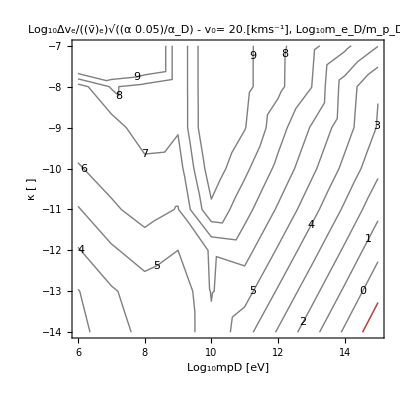

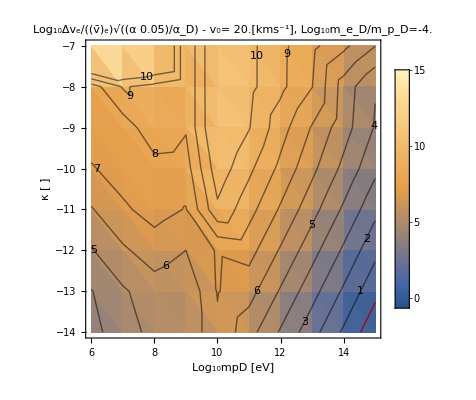

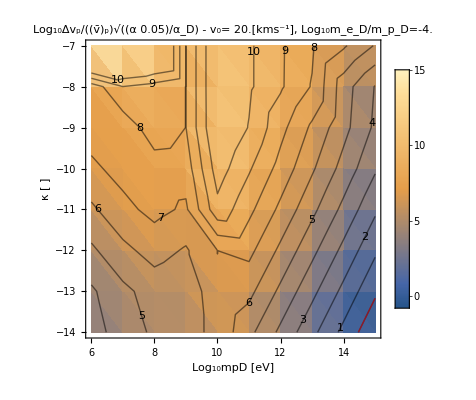

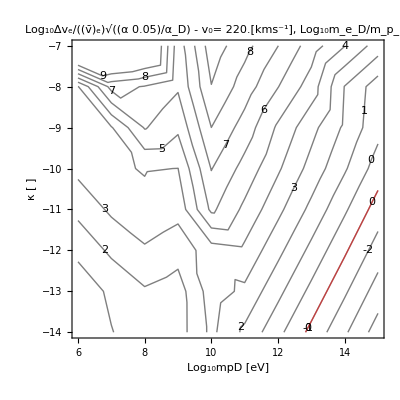

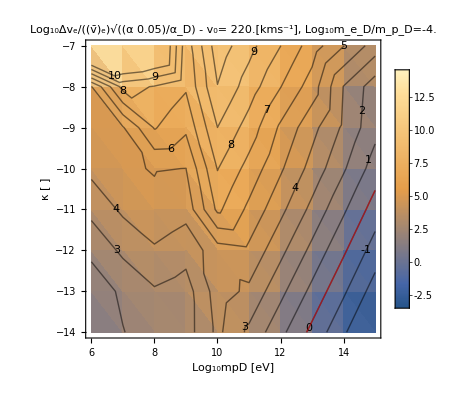

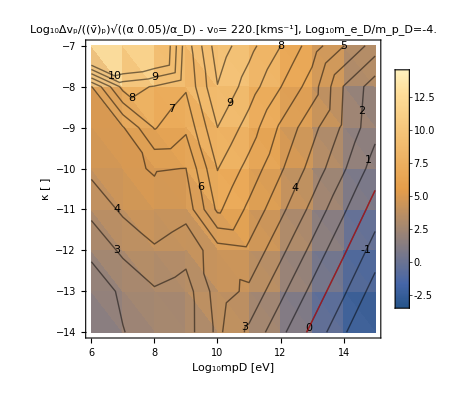

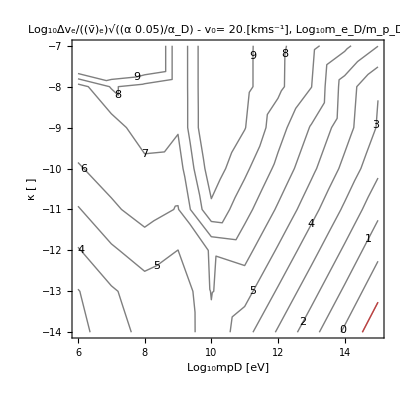

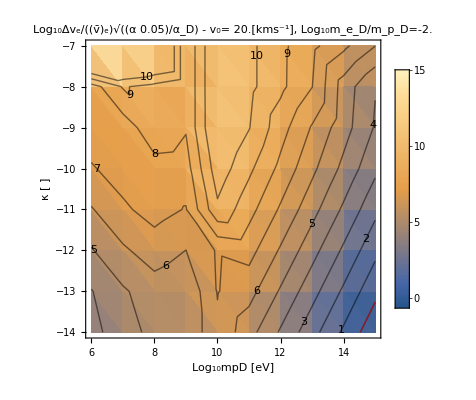

```mathematica
PlotKEchangeκContour[KEDictListMFPnoFF]
```

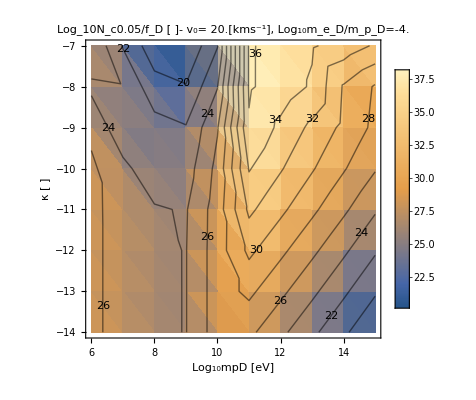

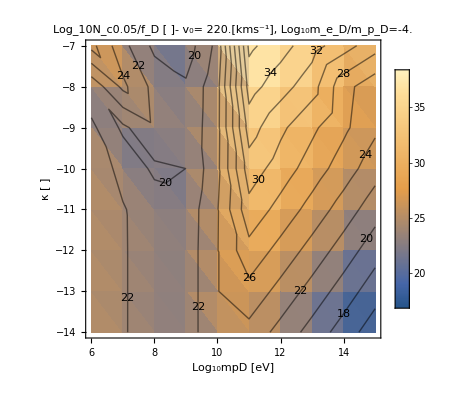

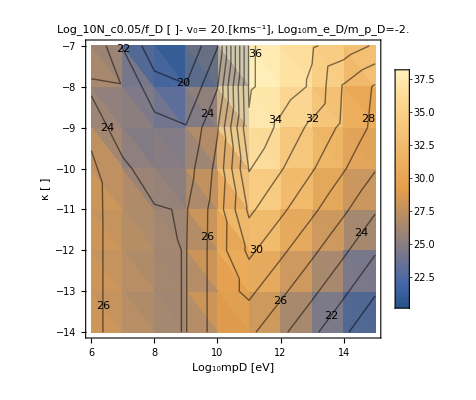

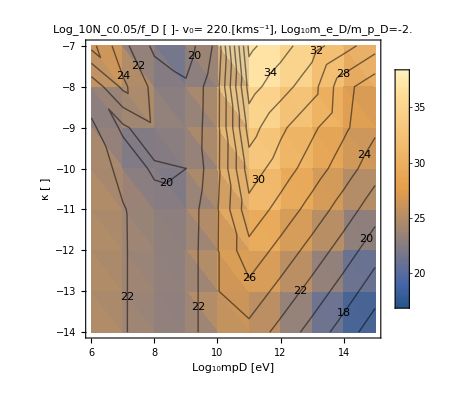

```mathematica
PlotNcκContour[KEDictListMFP]
```

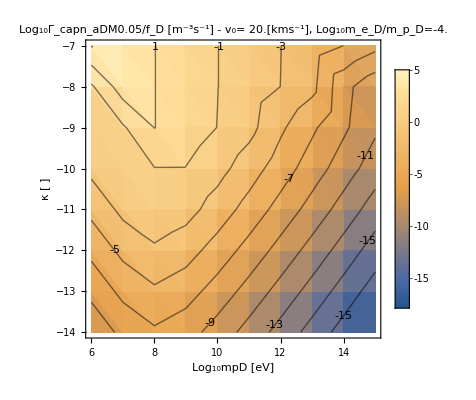

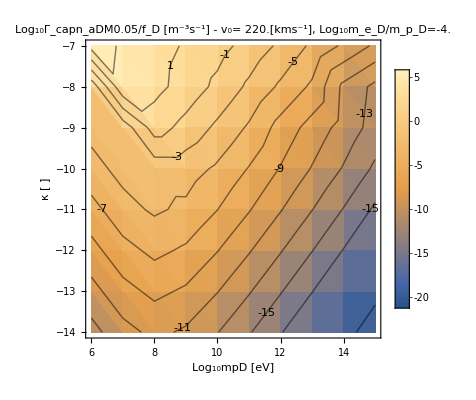

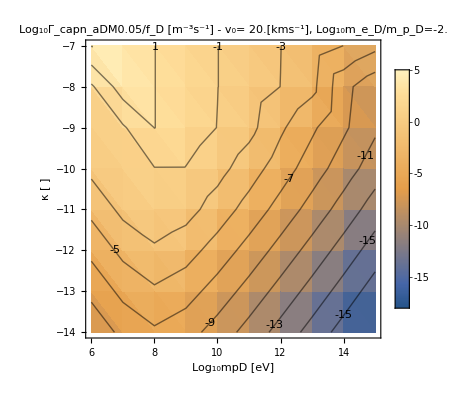

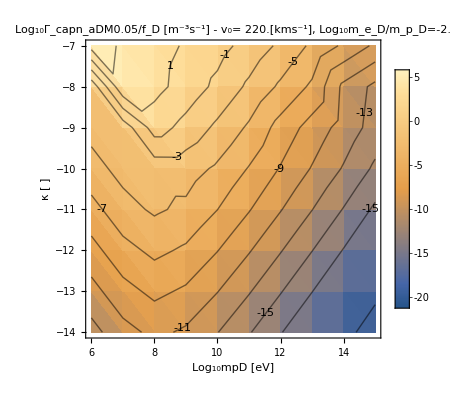

```mathematica
PlotCaptureRateκContour[KEDictListMFP]
```

I think the reason that the electronic evaporation rate drops off below 10^-10 κ is that at that point the MFP is less than the distance from the core to the surface. And since there is no electronic evaporation from the mantle, there is then no evaporation whatsoever. So I think this makes sense.

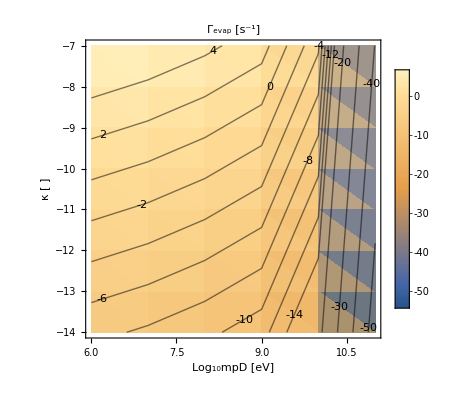

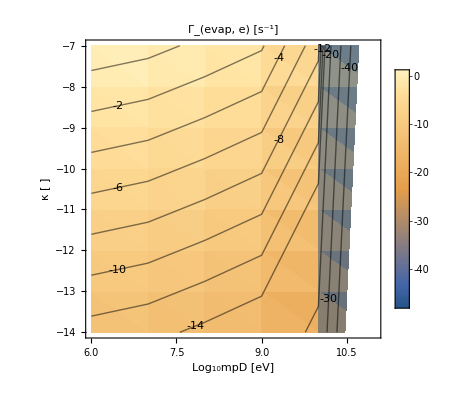

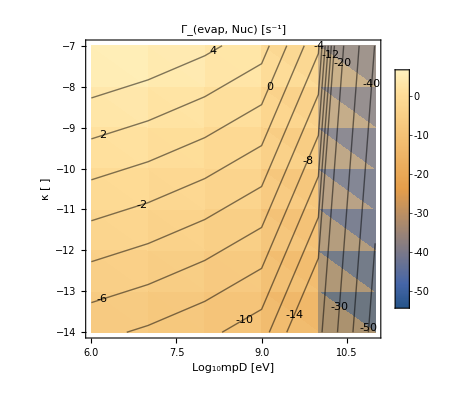

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
PlotEvaporationRateκContour[KEDictListMFPnoFF](*no MFP in evaporation, this shows that the change in rate is related to the evaporation volume. *)
```

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
"try computing the evaporation w MFP manually for fixed mass, say 10^6 eV. Comparing to the below plots should make it clear where the issue is. "
```

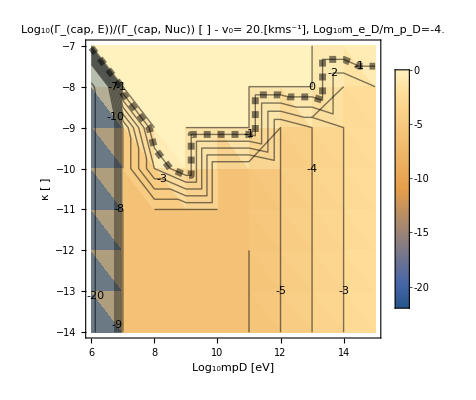

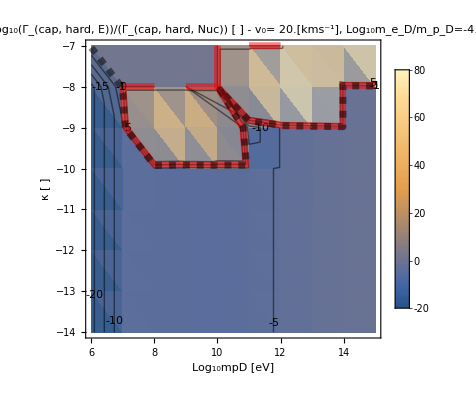

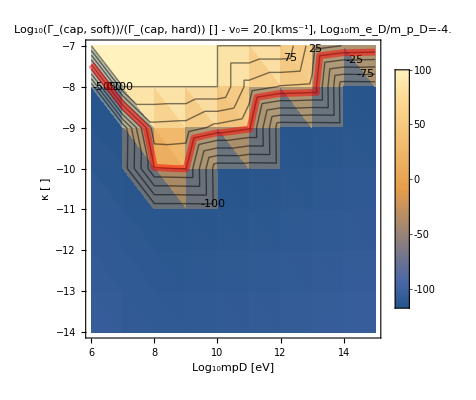

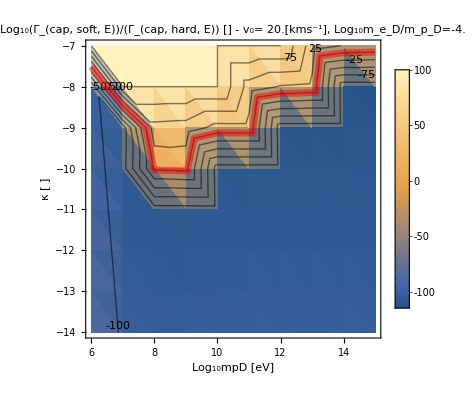

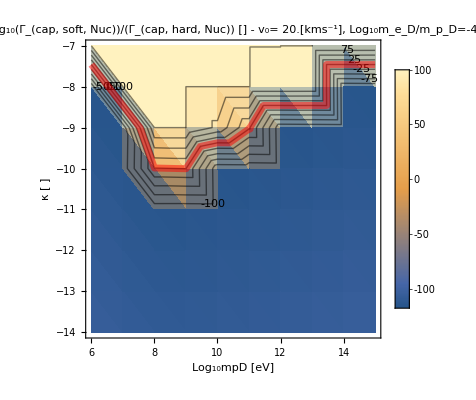

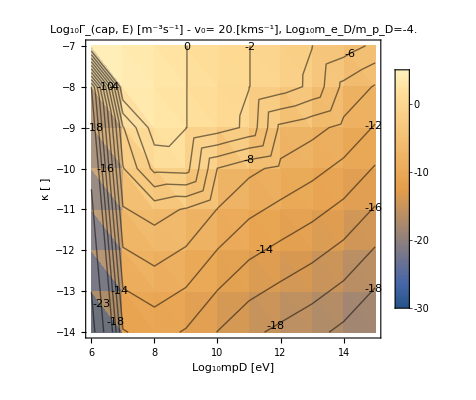

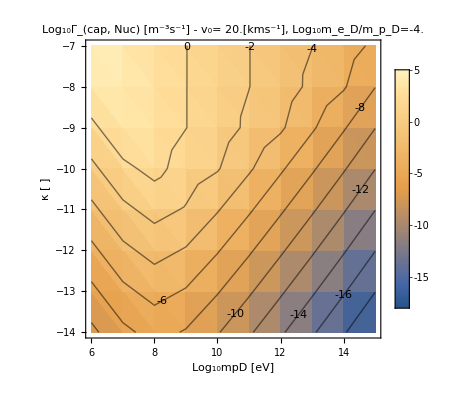

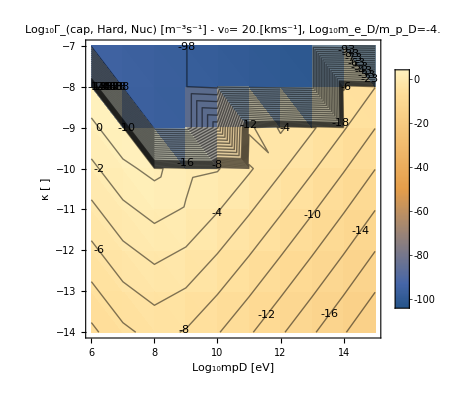

```mathematica
(*PlotCaptureRateComparison[PDictScansComparison]*)
PlotCaptureRateComparison[KEDictList]
```

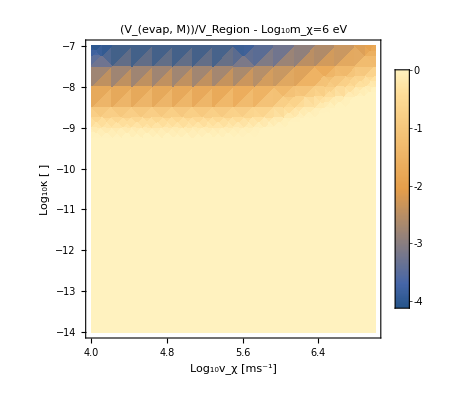

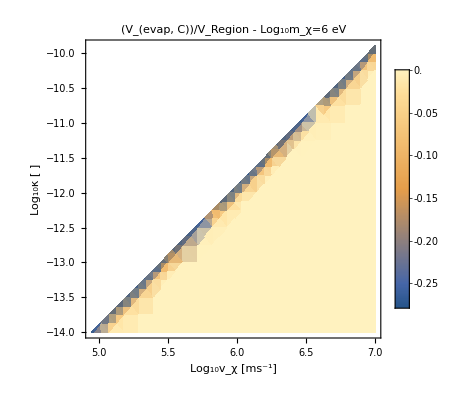

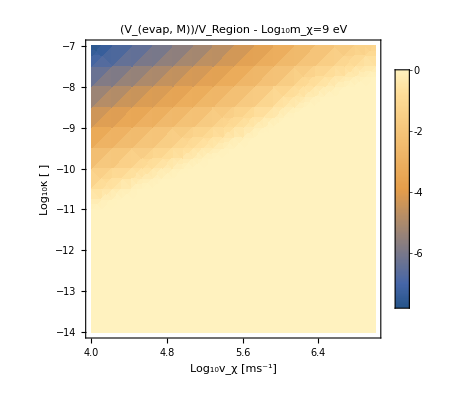

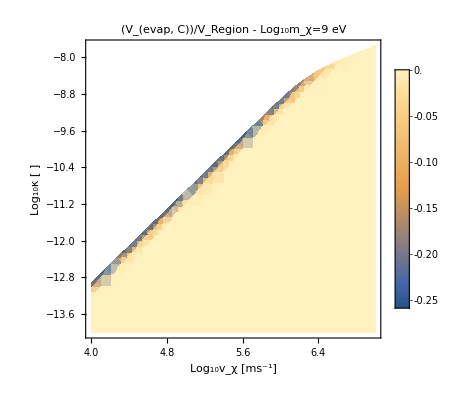

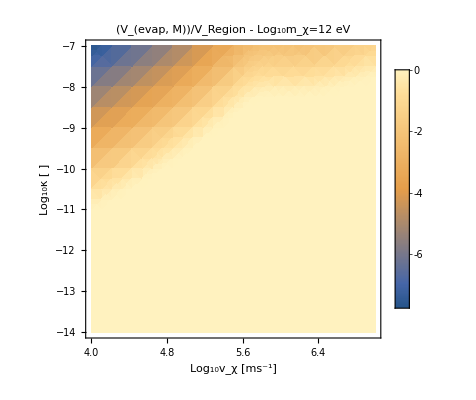

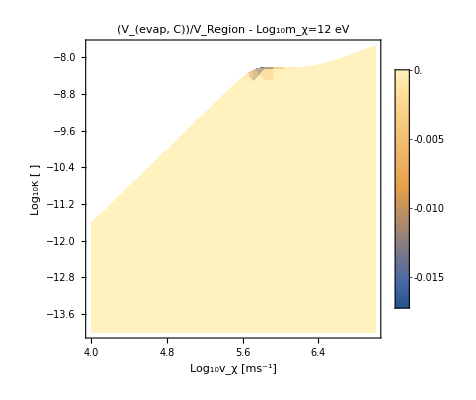

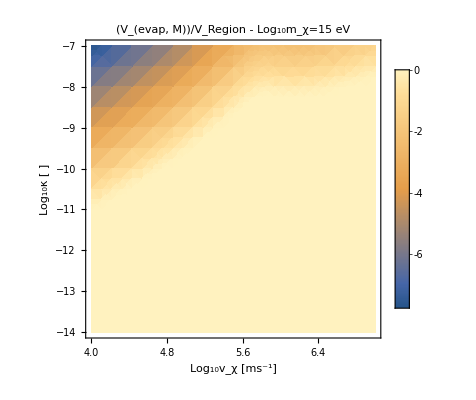

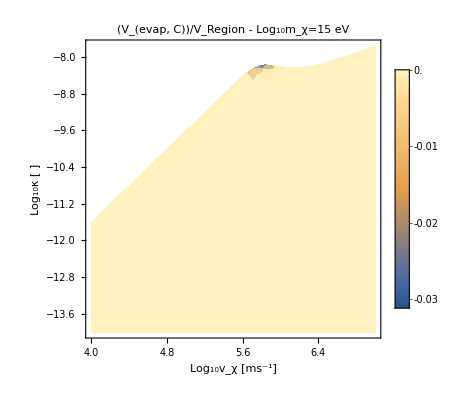

```mathematica
Do[
Print@DensityPlot[Log10@(1/((4π)/3(("rE")^3-("rcore")^3)/.EarthRepl)("Vevap"/.Function[{vχ,κ},EvaporationVolume[GetPenetrationDepthfnofv[vχ,ElectronicσDicts[[1+3m]],NuclearσDicts[[1+3m]]],κ,1]][10^Lvχ,10^Lκ])),{Lvχ,4,7},{Lκ,-14,-7},PlotRange->All,PlotLabel->"(V_(evap, M))/V_Region - Log_10m_χ="<>ToString[6+3 m]<>" eV",FrameLabel->{"Log_10v_χ [ms^-1]","Log_10κ [ ]"},PlotLegends->Automatic];

Print@DensityPlot[Log10@(1/((4π)/3("rcore")^3/.EarthRepl)("Vevap"/.Function[{vχ,κ},EvaporationVolume[GetPenetrationDepthfnofv[vχ,ElectronicσDicts[[1+3m]],NuclearσDictsnoFF[[1+3m]]],κ,2]][10^Lvχ,10^Lκ])),{Lvχ,4,7},{Lκ,-14,-7},PlotRange->All,PlotLabel->"(V_(evap, C))/V_Region - Log_10m_χ="<>ToString[6+3 m]<>" eV",FrameLabel->{"Log_10v_χ [ms^-1]","Log_10κ [ ]"},PlotLegends->Automatic],
{m,0,3}]
```

#### Get Scan Plots - full potential - w Volume evap Nuc and e - post capture fix

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

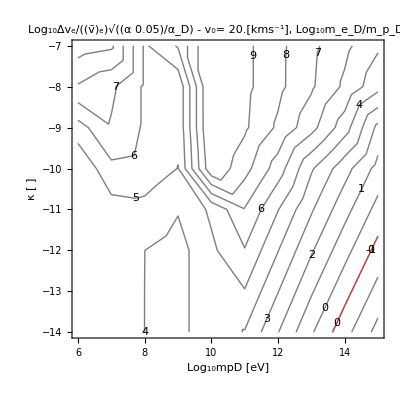

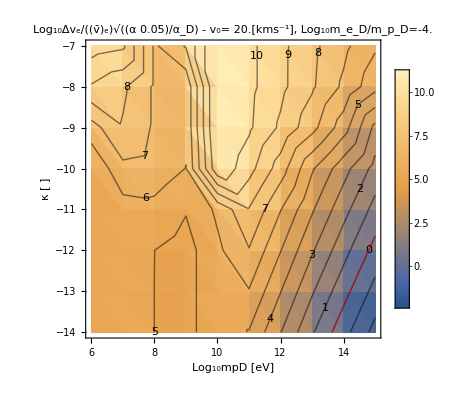

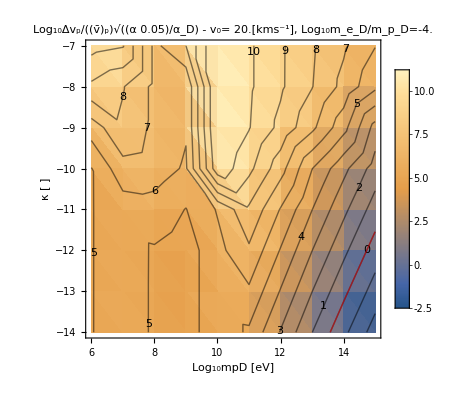

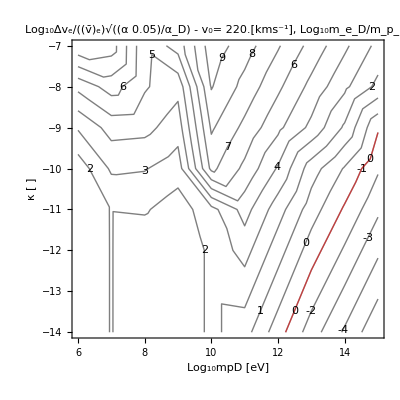

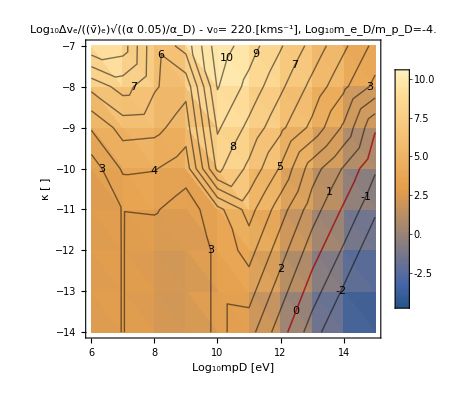

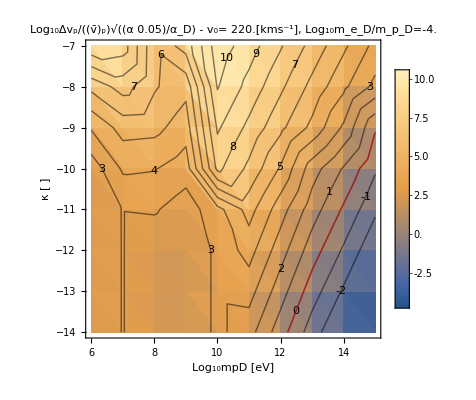

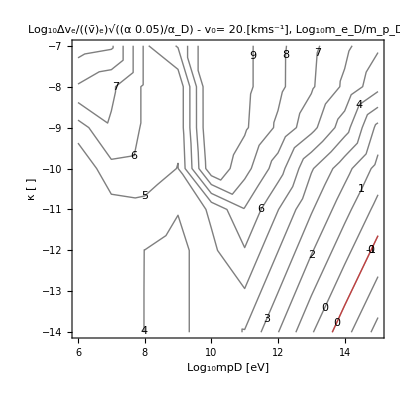

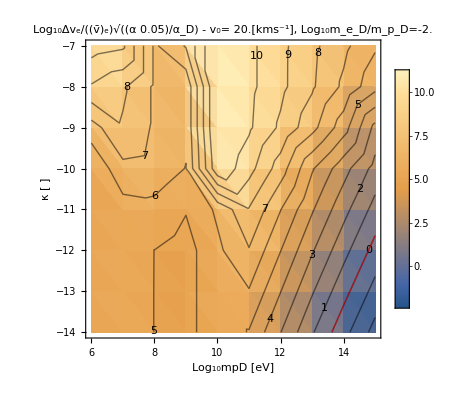

```mathematica
PlotKEchangeκContour[KEDictList]
```

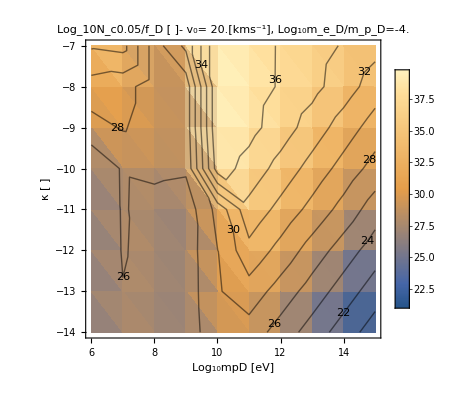

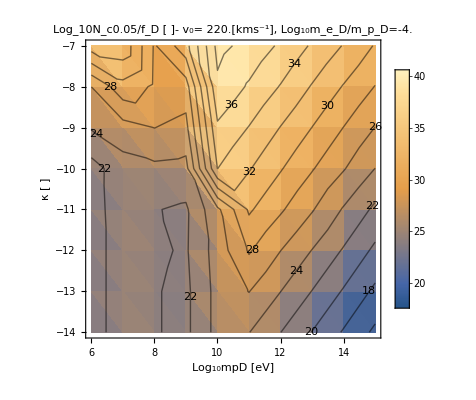

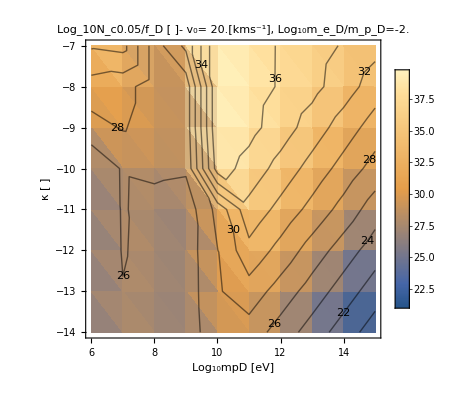

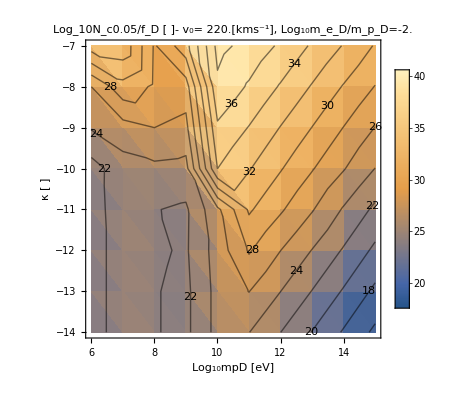

```mathematica
PlotNcκContour[KEDictList]
```

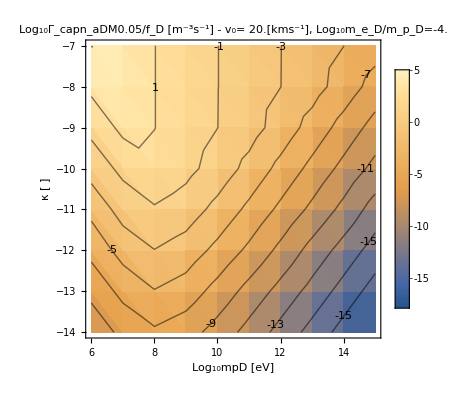

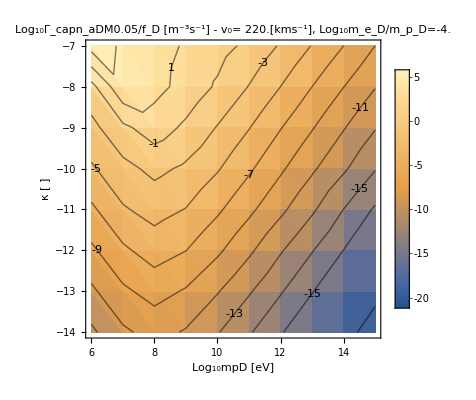

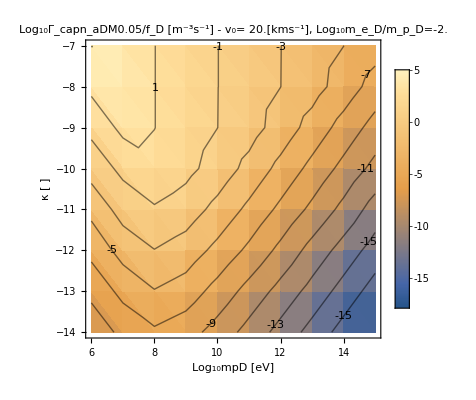

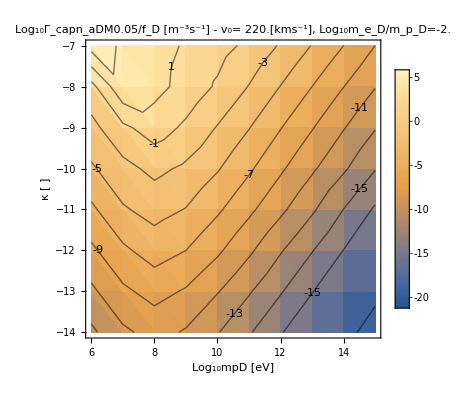

```mathematica
PlotCaptureRateκContour[KEDictList]
```

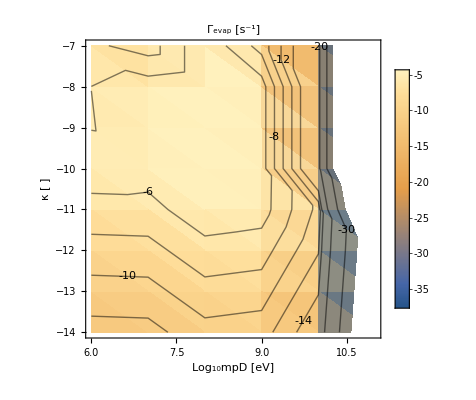

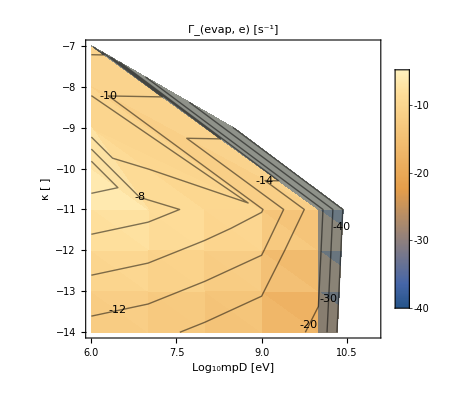

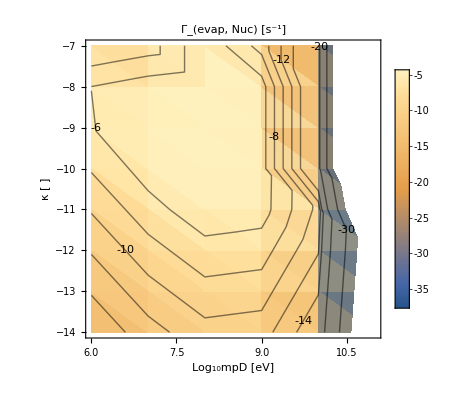

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - full potential - w Volume evap Nuc and e - ϕE=0.0015

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - full potential - w Volume evap Nuc and e - ϕE=0.15

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - full potential - w Volume evap Nuc and e - ϕEfrac=90%

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - full potential - w Volume evap Nuc and e - ϕEfrac=110% (w non-zero vE)

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
"
Features to understand: 
1) why is capture falling off so much at large and small velocities again?
2) is evaporation correct for nuclear? (why no recapture shelf?)
3) why is electronic capture exactly 0?
4) why doesn't hard capture shut off at 0 velocity for vesc^2<0?
"
```

#### Get Scan Plots - full potential - w Volume evap Nuc and e - w comparison of Nuc vs e

```mathematica
Dimensions@PDictScans
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScanscomparison[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScanscomparison]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotCaptureRateComparison[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«41 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - ϕE = 0, and non-zero vE

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
"you can have no ionization by increasing binding energy, but as soon as you have any ionization you don't know how much you have because Astrophysics - David to Yoni";
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - full potential - w Volume evap Nuc and e - ϕEfrac=110% (w non-zero vE) - post fix of capture rate

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

```mathematica
PlotNcκContour[KEDictList]
```

```mathematica
PlotCaptureRateκContour[KEDictList]
```

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
"
Features to understand: 
1) why is capture falling off so much at large and small velocities again?
2) is evaporation correct for nuclear? (why no recapture shelf?)
3) why is electronic capture exactly 0?
4) why doesn't hard capture shut off at 0 velocity for vesc^2<0?
"
```

```mathematica
ExportToDir[PDictScans,"PDictList_ϕE_110_pcnt.dat","PDictList"];
```

### Dark Electrons - not up to date, must be rerun

#### Interpolate over Electronic - Dark Electron sub MeV masses

```mathematica
FeσDicteeD=Monitor[Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeTotalparams[[i]],10,60,10^-6,4,True,True,2,ToString[StringForm["Fe ``",i]],False],{i,Length[FeTotalparams]}],{m,2,5}],m];(*note that 10^2 is 0.1 keV which is in tension with MPS bounds*)
SaveIt[NotebookDirectory[]<>"FeσDicteeD",FeσDicteeD]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

minimum energy requires relativistic probes, we won't consider these

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDicteeD.dat

```mathematica
SiO2σDicteeD=Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiO2Totalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["SiO2 ``",i]],False],{i,Length[SiO2Totalparams]}],{m,2,5}];
SaveIt[NotebookDirectory[]<>"SiO2σDicteeD",SiO2σDicteeD]
```

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

«1 more identical outputs»

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDicteeD.dat

```mathematica
MgOσDicteeD=Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,MgOTotalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["MgO ``",i]],False],{i,Length[MgOTotalparams]}],{m,2,5}];
SaveIt[NotebookDirectory[]<>"MgOσDicteeD",MgOσDicteeD]
```

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

«1 more identical outputs»

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDicteeD.dat

```mathematica
(*
FeσDicteeD=Delete[FeσDicteeD,-1];
SiO2σDicteeD=Delete[SiO2σDicteeD,-1];
MgOσDicteeD=Delete[MgOσDicteeD,-1];
SaveIt[NotebookDirectory[]<>"SiO2σDicteeD",SiO2σDicteeD]
SaveIt[NotebookDirectory[]<>"FeσDicteeD",FeσDicteeD]
SaveIt[NotebookDirectory[]<>"MgOσDicteeD",MgOσDicteeD]*)
```

```mathematica
FeσDicteeD=ReadIt[NotebookDirectory[]<>"FeσDicteeD"];
SiO2σDicteeD=ReadIt[NotebookDirectory[]<>"SiO2σDicteeD"];
MgOσDicteeD=ReadIt[NotebookDirectory[]<>"MgOσDicteeD"];
```

```mathematica
NADeleter=Delete[#,Position[#,"NA"]]&; (*For these light masses the minimal energy transfer*)
FeσDicteeD=NADeleter[FeσDicteeD];
MgOσDicteeD=NADeleter[MgOσDicteeD];
SiO2σDicteeD=NADeleter[SiO2σDicteeD];
```

```mathematica
ElectronicσDictseD=Gather[Flatten@Join[FeσDicteeD,SiO2σDicteeD,MgOσDicteeD],#1["mχ"]==#2["mχ"]&];
```

#### Interpolate over Nuclear - Dark Electron sub MeV masses

```mathematica
FeσDictNuceD=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeNucCoeffs,2,"Fe Nuc"],{m,2,5}];
SaveIt[NotebookDirectory[]<>"FeσDictNuceD",FeσDictNuceD]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuceD.dat

```mathematica
SiσDictNuceD=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiNucCoeffs,1,"Si Nuc"],{m,2,5}];
SaveIt[NotebookDirectory[]<>"SiσDictNuceD",SiσDictNuceD]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuceD.dat

```mathematica
MgσDictNuceD=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,MgNucCoeffs,1,"Mg Nuc"],{m,2,5}];
SaveIt[NotebookDirectory[]<>"MgσDictNuceD",MgσDictNuceD]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuceD.dat

```mathematica
OσDictNuceD=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiNucCoeffs,1,"O Nuc"],{m,2,5}];
SaveIt[NotebookDirectory[]<>"OσDictNuceD",OσDictNuceD]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuceD.dat

```mathematica
FeσDictNuceD=ReadIt[NotebookDirectory[]<>"FeσDictNuceD"];
SiσDictNuceD=ReadIt[NotebookDirectory[]<>"SiσDictNuceD"];
MgσDictNuceD=ReadIt[NotebookDirectory[]<>"MgσDictNuceD"];
OσDictNuceD=ReadIt[NotebookDirectory[]<>"OσDictNuceD"];
```

```mathematica
NuclearσDictseD=Gather[Flatten@Join[{FeσDictNuceD},{SiσDictNuceD},{MgσDictNuceD},{OσDictNuceD}],#1["mχ"]==#2["mχ"]&];
```

#### Scan over all masses

```mathematica
Clear[PDictScanseD]
PDictScanseD = {};
Do[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScaneD=ScanGetCapture[meDPoints,κpoints,v0Points,ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]],False];
AppendTo[PDictScanseD,PDictScaneD];
SaveIt[NotebookDirectory[]<>"PDictListeD",PDictScanseD];(*save after each mass point - it will overwrite as you go.*)
Clear[eind,Nucind,PDictScaneD];
,{m,6,15}]
(*SaveIt[NotebookDirectory[]<>"PDictListeD",PDictScanseD];*)
```

mχ: 1.×10^6

mpD: 1.×10^10

v0: 20000

βD: 8.42612×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^10

v0: 220000

βD: 6.96374×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^10

v0: 20000

βD: 8.42612×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^8

v0: 220000

βD: 6.89548×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^7

mpD: 1.×10^11

v0: 20000

βD: 8.42612×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^11

v0: 220000

βD: 6.96374×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^11

v0: 20000

βD: 8.42612×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^9

v0: 220000

βD: 6.89548×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^8

mpD: 1.×10^12

v0: 20000

βD: 8.42612×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^12

v0: 220000

βD: 6.96374×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^12

v0: 20000

βD: 8.42612×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^10

v0: 220000

βD: 6.89548×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^9

mpD: 1.×10^13

v0: 20000

βD: 8.42612×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^13

v0: 220000

βD: 6.96374×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^13

v0: 20000

βD: 8.42612×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^11

v0: 220000

βD: 6.89548×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^10

mpD: 1.×10^14

v0: 20000

βD: 8.42612×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^14

v0: 220000

βD: 6.96374×10^11

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^14

v0: 20000

βD: 8.42612×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^12

v0: 220000

βD: 6.89548×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^11

mpD: 1.×10^15

v0: 20000

βD: 8.42612×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^15

v0: 220000

βD: 6.96374×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^15

v0: 20000

βD: 8.42612×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^13

v0: 220000

βD: 6.89548×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^12

mpD: 1.×10^16

v0: 20000

βD: 8.42612×10^11

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^16

v0: 220000

βD: 6.96374×10^9

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^16

v0: 20000

βD: 8.42612×10^11

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^14

v0: 220000

βD: 6.89548×10^11

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^13

mpD: 1.×10^17

v0: 20000

βD: 8.42612×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^17

v0: 220000

βD: 6.96374×10^8

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^17

v0: 20000

βD: 8.42612×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^15

v0: 220000

βD: 6.89548×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^14

mpD: 1.×10^18

v0: 20000

βD: 8.42612×10^9

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^18

v0: 220000

βD: 6.96374×10^7

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^18

v0: 20000

βD: 8.42612×10^9

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^16

v0: 220000

βD: 6.89548×10^9

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^15

mpD: 1.×10^19

v0: 20000

βD: 8.42612×10^8

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^19

v0: 220000

βD: 6.96374×10^6

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^19

v0: 20000

βD: 8.42612×10^8

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^17

v0: 220000

βD: 6.89548×10^8

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

```mathematica
PDictScanseD=ReadIt[NotebookDirectory[]<>"PDictListeD"];
```

```mathematica
SaveIt[NotebookDirectory[]<>"PDictListeD",PDictScanseD];
```

#### Scan over extended range of masses for dark electrons

```mathematica
Clear[PDictScanseDTemp]
PDictScanseDTemp = {};
Do[eind = FirstPosition["mχ"/.ElectronicσDictseD,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDictseD,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScaneD=ScanGetCapture[meDPoints,κpoints,v0Points,ElectronicσDictseD[[eind]],NuclearσDictseD[[Nucind]],False];
AppendTo[PDictScanseDTemp,PDictScaneD];
SaveIt[NotebookDirectory[]<>"PDictListeDTemp",PDictScanseDTemp];(*save after each mass point - it will overwrite as you go.*)
Clear[eind,Nucind,PDictScaneD];
,{m,2,5}]
```

mχ: 100.

mpD: 1.×10^6

v0: 20000

βD: 8.42612×10^21

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^6

v0: 220000

βD: 6.96374×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^6

v0: 20000

βD: 8.42612×10^21

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 10000.

v0: 220000

βD: 6.89548×10^21

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1000.

mpD: 1.×10^7

v0: 20000

βD: 8.42612×10^20

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^7

v0: 220000

βD: 6.96374×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^7

v0: 20000

βD: 8.42612×10^20

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 100000.

v0: 220000

βD: 6.89548×10^20

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 10000.

mpD: 1.×10^8

v0: 20000

βD: 8.42612×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^8

v0: 220000

βD: 6.96374×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^8

v0: 20000

βD: 8.42612×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^6

v0: 220000

βD: 6.89548×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 100000.

mpD: 1.×10^9

v0: 20000

βD: 8.42612×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^9

v0: 220000

βD: 6.96374×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^9

v0: 20000

βD: 8.42612×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^7

v0: 220000

βD: 6.89548×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

```mathematica
SaveIt[NotebookDirectory[]<>"PDictListeDTemp",PDictScanseDTemp];
```

```mathematica
Table[AppendTo[PDictScanseD,PDictScanseDTemp[[i]]],{i,3,Length[PDictScanseDTemp]}];
```

```mathematica
"mχ"("c")^2/("JpereV")/.PDictScanseD/.SIConstRepl
```

{{{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6}},{{1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7},{1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7},{1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7},{1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7}},{{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8},{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8},{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8},{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8}},{{1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9},{1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9},{1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9},{1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9}},{{1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10},{1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10},{1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10},{1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10}},{{1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11},{1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11},{1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11},{1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11}},{{1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12},{1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12},{1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12},{1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12}},{{1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13},{1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13},{1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13},{1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13}},{{1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14},{1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14},{1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14},{1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14}},{{1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15},{1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15},{1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15},{1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15}},{{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.}},{{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.}}}

#### Rerun Computations on Existing PDicts

Want to change this to a module that replaces existing analysis for PDicts

```mathematica
Clear[PDictScansTemp]
PDictScansTemp= {};
Block[{NuclearσDictsList,pdicts,PDictind,Nucind,currentPDicts,Scandicts,analysiskeys,NcMaxdict,Ncdict,ScandictsKE},

NuclearσDictsList=Join[NuclearσDicts,NuclearσDictseD];

pdicts = PDictScanseD;

Monitor[
Do[
Print[p];
PDictind=FirstPosition["mχ"/.pdicts,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
currentPDicts = pdicts[[PDictind]];
Nucind = FirstPosition["mχ"/.NuclearσDictsList,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
Scandicts={};
Do[
analysiskeys={{"Pf"},{"PfE"},{"PfNuc"},{"intλinvE"},{"intλinvNuc"}};

Ncdict = currentPDicts[[d]];
Do[
NcMaxdict =GetNcMax[Ncdict,analysiskeys[[k]]];
Ncdict=GetNc[NcMaxdict,NuclearσDictsList[[Nucind]],analysiskeys[[k]]];
,{k,Length[analysiskeys]}];

AppendTo[Scandicts,Ncdict];
,{d,Length[currentPDicts]}];

ScandictsKE=IterateKEchange[Flatten@Scandicts,{0.05},"α"/.Constants`SIConstRepl];

AppendTo[PDictScansTemp,ScandictsKE]

,{p,4,15}]
,p]
]
PDictScanseD=PDictScansTemp;
ClearAll[PDictScansTemp]

(*SaveIt[NotebookDirectory[]<>filenames[[p-5]],Scandicts]*)
```

4

5

6

7

8

9

10

11

12

13

14

15

```mathematica
"mχ"("c")^2/("JpereV")/.PDictScanseD/.SIConstRepl
```

{{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7},{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8},{1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9},{1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10},{1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11},{1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12},{1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13},{1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14},{1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15},{{100.,100.,100.,100.,100.,100.,100.,100.},{100.,100.,100.,100.,100.,100.,100.,100.},{100.,100.,100.,100.,100.,100.,100.,100.},{100.,100.,100.,100.,100.,100.,100.,100.}},{{1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.},{1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.},{1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.},{1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.}},{{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.}},{{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.}}}

#### Get Scan Plots

```mathematica
KEDictListeD = Table[IterateKEchange[Flatten@PDictScanseD[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScanseD]}];
```

```mathematica
PlotKEchangeκContour[KEDictListeD]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictListeD]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictListeD]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictListeD]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
(*PlotCaptureRateComparison[PDictScansComparison]*)
PlotCaptureRateComparison[KEDictListeD]
```

-Graphics-

-Graphics-

-Graphics-

«41 more identical outputs»

#### Get Scan Plots - smaller range for GuineaPig

```mathematica
Dimensions[KEDictListeD]
```

{10,32}

```mathematica
PlotKEchangeκContour[KEDictList[[5;;]]]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotKEchangeκContour[KEDictListeD[[;;6]]]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictListeD[[;;6]]]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictListeD[[;;6]]]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## Scrap